```mathematica
coor2D=#-Threaded@Mean@#&@{{-1,0},{1,0},{0,√3}};
style={"M"->Darker@Green(*RGBColor[{0.317649521687249, 0.4537678120460686, 0.6815169959761883, 1.}]*),"F"->Red(*RGBColor[{0.8091570166958525, 0.497131467100969, 0.33226727100135117, 1.}]*),"C"->Purple(*RGBColor[{0.5472323475533841, 0.7723049500262382, 0.4403195729684779, 1.}]*),"U"->RGBColor[{0.317649521687249, 0.4537678120460686, 0.6815169959761883, 1.}]};
{celltypes,colors}={#,RGBColor[Mean[DeleteCases[Flatten[ImageData[#],1],{1.,1.,1.,1.}]]]&/@#}&@{-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
fnMI=SortBy[FileNames["/Users/Avimayo/Library/CloudStorage/Box-Box/shoval/double reporter/dblrep analysis days 1-14 110523/export/*detections.xlsx"],StringSplit[FileBaseName[#],"_"][[2]]&];
```

```mathematica
fnTAC=Most@SortBy[FileNames["/Users/Avimayo/Library/CloudStorage/Box-Box/shoval/double reporter/dblrep analysis TAC:Sham day 28 (100324)/TAC:SHAM dblrep analysis files/export/*detections.xlsx"],StringSplit[FileBaseName[#],"_"][[2]]&];
```

```mathematica
fnMITAC=FileNames["/Users/Avimayo/Library/CloudStorage/Box-Box/shoval/double reporter/dblrep analysis MI: TAC:Sham day 28 (200324)/export/*_detections.xlsx"];
```

```mathematica
TableForm/@(Join@@(GatherBy[FileBaseName/@#,StringSplit[#,"_"][[-2]]&]&/@{fnMI,fnTAC,fnMITAC}))
```

{202.tiff - 202_02d_detections
222.tiff - 222_02d_detections
227.tiff - 227_02d_detections
228.tiff - 228_02d_detections,204.tiff - 204_04d_detections
207.tiff - 207_04d_detections
215.tiff - 215_04d_detections
217.tiff - 217_04d_detections,185.tiff - 185_07d_detections
191.tiff - 191_07d_detections
193.tiff - 193_07d_detections
201.tiff - 201_07d_detections,195.tiff - 195_14d_detections
197.tiff - 197_14d_detections
200.tiff - 200_14d_detections,176.tiff - 176_sham_detections
194.tiff - 194_sham_detections,275 TAC.tiff - 275 TAC_detections,278 SHAM.tiff - 278 SHAM_detections,280 SHAM.tiff - 280 SHAM_detections,283 TAC.tiff - 283 TAC_detections,284 TAC.tiff - 284 TAC_detections,286 TAC.tiff - 286 TAC_detections,289 SHAM.tiff - 289 SHAM_detections,290 SHAM.tiff - 290 SHAM_detections,MI_165.tiff - MI_165_28d_detections
MI_166.tiff - MI_166_28d_detections
MI_171.tiff - MI_171_28d_detections
MI_175.tiff - MI_175_28d_detections
MI_176.tiff - MI_176_28d_detections
MI_177.tiff - MI_177_28d_detections
MI_179.tiff - MI_179_28d_detections
MI_182.tiff - MI_182_28d_detections
MI_183.tiff - MI_183_28d_detections,TAC_282.tiff - TAC_282_detections,TAC_285.tiff - TAC_285_detections}

```mathematica
dataMI=Import[#,"Data"][[1,3;;,{1,5,3,7,8}]]&/@fnMI;
```

```mathematica
dataTAC=Import[#,"Data"][[1,3;;,{1,6,5,8,9}]]&/@fnTAC;
```

```mathematica
dataMITAC=((Import[#,"Data"][[1,3;;,{1,6,5,8,9}]]&/@fnMITAC)/.(StringDrop[FileBaseName[#],-15]->StringDelete[StringDrop[FileBaseName[#],-11],"MI_"]&/@fnMITAC))/.{"PVFibrosis 3"->"PV Fibrosis 3","PVFibrosis 2"->"PV Fibrosis 2","PVFibrosis 1"->"PV Fibrosis 1"};
```

```mathematica
dataMI[[7]]=Join@@(#[[1]]/."ToAnalyze"->#[[2]]&/@({FindClusters[#[[;;,{4,5}]]->#,6]&@dataMI[[7]],{"RZ1","RZ2","RZ3","IZ1","IZ2","IZ3"}}ᵀ));
```

```mathematica
dataMI[[9]]==dataMI[[9]]/."RZ2"->"IZ3";
```

```mathematica
dataJoined=Delete[
(Join@@(GatherBy[#,#[[2]]&]&/@Join[dataMI,dataTAC,dataMITAC]))/.{"cTnT"->"C","GFP"->"M","TdTom"->"F","Other"->"U"},
{55}];
```

```mathematica
DeleteCases[((Join@@(GatherBy[#,#[[2]]&]&/@Join[dataMI,dataTAC,dataMITAC]))/.{"cTnT"->"C","GFP"->"M","TdTom"->"F","Other"->"U"})[[55]],{___,"Other",___}][[;;,2]]//Union
```

{RZ2}

```mathematica
NCounts=ParallelMap[
{Sequence@@(StringSplit[StringSplit[#[[1,1]],"- "][[2]]/."176_ sham"->"176_sham"," "|"_"]),#[[1,2]],
Table[
{r[[1]],Sequence@@{#,Total@#}&@Table[Count[#,c],{c,{"F","M","C","U"}}]&@Select[r[[2]][#[[2;;]]]&][#][[;;,1]]},
{r,{#[[1]],RegionMember[Region[Disk[#[[2;;]],50]]]}&/@#}]&@DeleteCases[#[[;;,3;;]],{"U",__}]}&,
dataJoined]/.{"TAC",x_,y_,z_}:>{x,"TAC",y,z};
```

```mathematica
NCountsNoU=ParallelMap[
{Sequence@@(StringSplit[StringSplit[#[[1,1]],"- "][[2]]/."176_ sham"->"176_sham"," "|"_"]),#[[1,2]],
Table[
{r[[1]],Sequence@@{#,Total@#}&@Table[Count[#,c],{c,{"C","M","F"}}]&@Select[r[[2]][#[[2;;]]]&][#][[;;,1]]},
{r,{#[[1]],RegionMember[Region[Disk[#[[2;;]],50]]]}&/@#}]&@#[[;;,3;;]]}&,
DeleteCases[dataJoined,{___,"U",___},2]]/.{"TAC",x_,y_,z_}:>{x,"TAC",y,z};
```

```mathematica
rule={
x_?(Quiet@StringContainsQ[#,"Fibrosis"]&):>StringSplit[x," "][[1]],
x_?(Quiet@StringContainsQ[#,"RZ"]&):>StringTake[x,2],
x_?(Quiet@StringContainsQ[#,"IZ"]&):>StringTake[x,2],
x_?(Quiet@StringContainsQ[#,"PV Sham"]&):>StringTake[x,7],
x_?(Quiet@StringContainsQ[#,"Suture"]&):>"Suture"};
```

```mathematica
NCountsNoUSorted=DeleteCases[NCountsNoU,{"176","28d",__}]/.{y:("166"|"175"|"179"),"28d",x_,z_}:>{y,"sham",x,z}(*/.rule*);
```

```mathematica
TableForm[({#[[1,1]],{#[[1,1]],{#[[1,1]],#[[;;,2]]}&/@GatherBy[Rest/@#,First]}&/@GatherBy[Rest/@#,First]}&/@GatherBy[DeleteCases[Flatten[{#[[{2,1,3}]],Length@#[[4]]}]&/@NCountsNoUSorted/.rule/.{"SHAM"->"Sham_TAC","sham"->"Sham_MI"},{"2d"|"4d"|"7d"|"14d"|"28",_,"RZ",_}],First])[[{5,1,2,3,4,8,7,6}]],TableDepth->6]
```

Sham_MI | 176 | RZ | {574,536,680}
194 | RZ | {547,638,529}
166 | RZ | {360,415,385}
175 | RZ | {468,497,492}
179 | RZ | {367,459,489}
2d | 202 | IZ | {121,281,489}
222 | IZ | {34,196,44}
227 | IZ | {686,631,585}
228 | IZ | {483,424,376}
4d | 204 | IZ | {74,24,197}
207 | IZ | {241,243,207}
215 | IZ | {195,218,776}
217 | IZ | {681,695,555}
7d | 185 | IZ | {713,937}
191 | IZ | {789,684}
193 | IZ | {621,526,710}
201 | IZ | {395,994,798}
14d | 195 | IZ | {956,772}
197 | IZ | {201,244,476}
200 | IZ | {615,878,271}
28d | 165 | IZ | {508,419,513,432}
Suture | {867,666,507}
RZ | {478,632,370}
171 | IZ | {301,324,398,238}
Suture | {359,344}
RZ | {373,452,378}
177 | IZ | {448,394}
Suture | {678,599,266}
RZ | {414,256,444}
182 | IZ | {867,889,231}
Suture | {449}
RZ | {346,210,666}
183 | IZ | {327,486,490,869}
Suture | {510}
RZ | {392,361,520}
Sham_TAC | 278 | RZ | {356,354,376,441,386}
PV Sham | {265,260,366}
280 | RZ | {399,353,299,391,246}
PV Sham | {286,219,417}
289 | RZ | {317,504,428,466,411}
PV Sham | {402,366,384}
290 | RZ | {261,299,225,426,394}
PV Sham | {218,235,368}
TAC | 275 | Low | {592,563,540}
High | {781,578,760,552}
PV | {302,328,336}
283 | Low | {499,596,538,369}
High | {372,592,365}
PV | {325,385,217}
284 | High | {609,617,497}
Low | {329,416,206}
PV | {229,178,522}
286 | High | {518,602,338}
Low | {399,366,509}
PV | {280,238,244}
282 | High | {1073}
Low | {573,362,535}
PV | {442,360,473}
285 | High | {588}
Low | {362,325,452}
PV | {323,232,367}

```mathematica
counts={#[[1,1,2]],{#[[1,1]],Mean@#[[;;,2]]}&/@GatherBy[Join@@#[[;;,2]],First]}&/@GatherBy[
Map[
{#[[1,;;2]],{#[[1,1]],MeanAround/@(#[[;;,2]]ᵀ)}&/@GatherBy[#[[;;,3;;]],#[[1]]&]}&,
GatherBy[
{Sequence@@#[[;;3]],{"C","M","F"}/.Rule@@@Tally@#[[4,;;,1]]/._String:>0}&/@NCountsNoUSorted/.rule,
#[[;;2]]&]
],
#[[1,2]]&];
```

```mathematica
counts1=Transpose/@Map[Transpose,({#[[1,1,2]],{#[[1,1]],#[[;;,2]]}&/@GatherBy[Join@@#[[;;,2]],First]}&/@GatherBy[
Map[
{#[[1,;;2]],{#[[1,1]],MeanAround/@(#[[;;,2]]ᵀ)}&/@GatherBy[#[[;;,3;;]],#[[1]]&]}&,
GatherBy[
{Sequence@@#[[;;3]],{"C","M","F"}/.Rule@@@Tally@#[[4,;;,1]]/._String:>0}&/@NCountsNoUSorted/.rule,
#[[;;2]]&]
],
#[[1,2]]&])[[{1,2,3,4,-1},2,;;,2]],{2}]/.Around[x_,y_]:>x//N;
```

```mathematica
TableForm[
Round[Join@@{Most@counts1/.x:{{_Real..},{_Real..}}:>DistributionFitTest[x[[1]],x[[2]],{"TestData","KolmogorovSmirnov"}],
Last@counts1/.x:{{_Real..},{_Real..},{_Real..}}:>(DistributionFitTest[#[[1]],#[[2]],{"TestData","KolmogorovSmirnov"}]&/@Subsets[x,{2}])},.001],
TableHeadings->{{"2d:IZ~RZ","4d:IZ~RZ","7d:IZ~RZ","14d:IZ~RZ","28d:IZ~RZ","28 suture:IZ~RZ","28d:IZ~28 suture"},{"C","M","F"}},TableDepth->2]
```

| C | M | F
2d:IZ~RZ | {0.75,0.229} | {0.75,0.229} | {0.5,0.429}
4d:IZ~RZ | {1.,0.029} | {1.,0.029} | {1.,0.029}
7d:IZ~RZ | {1.,0.029} | {1.,0.029} | {1.,0.029}
14d:IZ~RZ | {1.,0.1} | {1.,0.1} | {1.,0.1}
28d:IZ~RZ | {0.6,0.357} | {1.,0.008} | {1.,0.008}
28 suture:IZ~RZ | {1.,0.008} | {1.,0.008} | {1.,0.008}
28d:IZ~28 suture | {0.6,0.357} | {1.,0.008} | {1.,0.008}

```mathematica
TableForm[
Round[#,.001]&@({counts1[[3,;;,1]],#}ᵀ&/@Append[counts1[[{1,2,4,5},;;,1]],counts1[[5,2]]]/.x:{{_Real..},{_Real..}}:>DistributionFitTest[x[[1]],x[[2]],{"TestData","KolmogorovSmirnov"}])ᵀ,TableHeadings->{{"C","M","F"},{"2d:IZ~7d:IZ","4d:IZ~7d:IZ","14d:IZ~7d:IZ","28d:IZ~7d:IZ","28 suture~7d:IZ"}},TableDepth->2,TableDirections->Row,TableAlignments->{Center, Center}]
```

| C | M | F
2d:IZ~7d:IZ | {1.,0.029} | {1.,0.029} | {1.,0.029}
4d:IZ~7d:IZ | {0.5,0.771} | {1.,0.029} | {0.75,0.229}
14d:IZ~7d:IZ | {0.333,0.971} | {1.,0.057} | {0.333,0.971}
28d:IZ~7d:IZ | {0.25,0.992} | {1.,0.016} | {0.5,0.563}
28 suture~7d:IZ | {0.75,0.143} | {0.55,0.429} | {1.,0.016}

{2d,4d,7d,14d,28d}

{{IZ,RZ},{IZ,RZ},{IZ,RZ},{IZ,RZ},{IZ,RZ}}

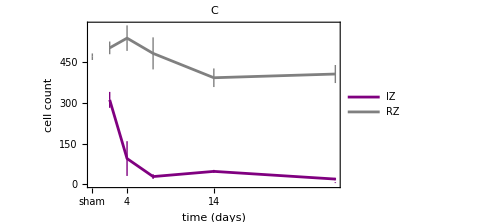
-Graphics--Graphics--Graphics-

```mathematica
counts[[{1,2,3,4,-1},1]]
counts[[{1,2,3,4,-1},2,{1,-1},1]]
Row[
MapIndexed[
ListLinePlot[#,PlotStyle->{{Purple,Darker@Green,Red}[[#2[[1]]]],{Gray,Thin}},Frame->True,Axes->False,ImageSize->Medium,FrameTicks->{{Automatic,None},{{{0,"sham"},2,4,7,14,28},None}},FrameLabel->{"time (days)","cell count"},PlotLabel->{"C","M","F"}[[#2[[1]]]],PlotLegends->Placed[{"IZ","RZ"},Bottom]]&,Join[{{2,4,7,14,28},#}ᵀ&/@#[[;;2]],{{Callout[{28,#[[3]]},"Suture",LabelVisibility->∞]},{Callout[{0,#[[4]]},"sham"]}}]&/@(Join@@@({((Transpose/@(counts[[{1,2,3,4,-1},2,{1,-1},2]]ᵀ))ᵀ),{#}&/@counts[[-1,2,2,2]],{#}&/@counts[[5,2,1,2]]}ᵀ))],Spacer@10]
```

```mathematica
Row[
MapIndexed[
ListLinePlot[{#[[1]],{#[[4,1]],#[[1,1]]},#[[3]]},PlotStyle->{{Purple,Darker@Green,Red}[[#2[[1]]]],{Dashed,{Purple,Darker@Green,Red}[[#2[[1]]]]},{Purple,Darker@Green,Red}[[#2[[1]]]]},Frame->True,Axes->False,ImageSize->Medium,FrameTicks->{{Automatic,None},{{(*{0,"sham"},*)2,4,7,14,28},None}},FrameLabel->{"time (days)","cell count"},PlotLabel->{"C","M","F"}[[#2[[1]]]],PlotRange->{{-.1,30},All}]&,Join[{{2,4,7,14,28},#}ᵀ&/@#[[;;2]],{{Callout[{28,#[[3]]},"Suture",LabelVisibility->All]},{Callout[{0,#[[4]]},"sham",LabelVisibility->All]}}]&/@(Join@@@({((Transpose/@(counts[[{1,2,3,4,-1},2,{1,-1},2]]ᵀ))ᵀ),{#}&/@counts[[-1,2,2,2]],{#}&/@counts[[5,2,1,2]]}ᵀ))],Spacer@10]
```

-Graphics--Graphics--Graphics-

```mathematica
Fractions={#[[1,;;2]],Sort[{#[[1,1]],((N@((#[[;;2]])/(Total@#))&/@#[[;;,2]])ᵀ)}&/@GatherBy[#[[;;,3;;]],#[[1]]&]]}&/@GatherBy[({Sequence@@#[[;;3]],Table[Count[#[[4,;;,1]],c],{c,{"F","M","C"(*,"U"*)}}]}&/@NCounts)/.{
x_?(Quiet@StringContainsQ[#,"Fibrosis"]&):>StringSplit[x," "][[1]],
x_?(Quiet@StringContainsQ[#,"RZ"]&):>StringTake[x,2],
x_?(Quiet@StringContainsQ[#,"IZ"]&):>StringTake[x,2],
x_?(Quiet@StringContainsQ[#,"PV Sham"]&):>StringTake[x,7],
x_?(Quiet@StringContainsQ[#,"Suture"]&):>"Suture"},#[[;;2]]&];
```

```mathematica
NeighborhoodCounts={#[[1,1,1]],{#[[1,2]],#[[2]]}&/@#}&/@GatherBy[{#[[1,1]],Mean@#[[;;,2]]}&/@GatherBy[{#[[{2,3}]],Around[Mean@#,StandardDeviation@#]&/@(#[[4,;;,2]]ᵀ)}&/@NCountsNoUSorted/.rule,#[[1]]&],#[[1,1]]&];
```

```mathematica
NeighborhoodCounts1=({#[[1,1,1]],{#[[1,2]],#[[2]]ᵀ}&/@#}&/@GatherBy[{#[[1,1]],#[[;;,2]]}&/@GatherBy[{#[[{2,3}]],Around[Mean@#,StandardDeviation@#]&/@(#[[4,;;,2]]ᵀ)}&/@NCountsNoUSorted/.rule,#[[1]]&],#[[1,1]]&]/.Around[x_,y_]:>x//N);
```

```mathematica
NeighborhoodCounts1PerAnimal={#[[1,1,1]],{#[[1,1]],#[[;;,2]]}&/@GatherBy[{#[[1,2]],#[[2]]}&/@#,#[[1]]&]}&/@GatherBy[{#[[1,2;;3]],Mean@#[[;;,4]]}&/@GatherBy[NCountsNoUSorted/.rule/.x:{{_,{_Integer..},_}..}:>(Mean@N@x[[;;,2,;;3]]),#[[;;3]]&],
#[[1,1]]&];
```

```mathematica
NeighborhoodCounts1PerAnimalPercent={#[[1,1,1]],{#[[1,1]],#[[;;,2]]}&/@GatherBy[{#[[1,2]],#[[2]]}&/@#,#[[1]]&]}&/@GatherBy[{#[[1,2;;3]],Mean@#[[;;,4]]}&/@GatherBy[NCountsNoUSorted/.x:{_Integer..}:>N@(x/(Total@x))/.rule/.x:{{_,{_Real..},_}..}:>(Mean@N@x[[;;,2,;;3]]),#[[;;3]]&],
#[[1,1]]&];
```

```mathematica
Export["MI_TAC.xls","Sheets"->(#[[1]]->Prepend[Join@@(Prepend[#[[2]],{#[[1]]}]&/@#[[2]]),{"C","M","F"}]&/@(NeighborhoodCounts1PerAnimal[[{5,1,2,3,4,8,6,7}]]/.{"sham"->"Sham_MI","SHAM"->"Sham_TAC"})),"Rules"]
```

MI_TAC.xls

```mathematica
Export["MI_TAC%.xls","Sheets"->(#[[1]]->Prepend[Join@@(Prepend[#[[2]],{#[[1]]}]&/@#[[2]]),{"C","M","F"}]&/@(NeighborhoodCounts1PerAnimalPercent[[{5,1,2,3,4,8,6,7}]]/.{"sham"->"Sham_MI","SHAM"->"Sham_TAC"})),"Rules"]
```

MI_TAC%.xls

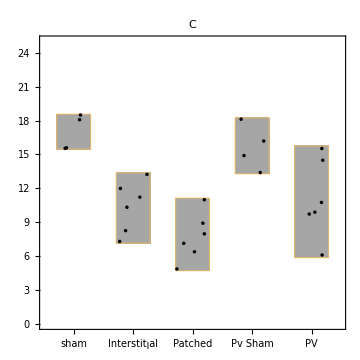
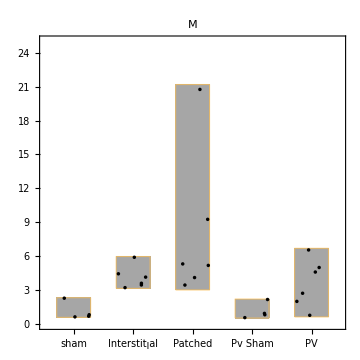
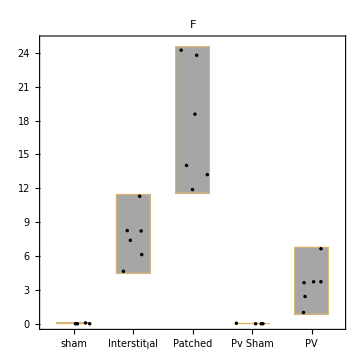
-Graphics-
 | ES | p-val
sham/Interstitןal | 0. | 0.
sham,Patched | 0. | 0.
Interstitןal/Patched | 6. | 0.0411255
Pv Sham/Sham | 3. | 0.0380952-Graphics-
 | ES | p-val
sham/Interstitןal | 0. | 0.
sham,Patched | 0. | 0.
Interstitןal/Patched | 10. | 0.179654
Pv Sham/Sham | 4. | 0.0666667-Graphics-
 | ES | p-val
sham/Interstitןal | 0. | 0.
sham,Patched | 0. | 0.
Interstitןal/Patched | 0. | 0.
Pv Sham/Sham | 0. | 0.

```mathematica
Row[MapIndexed[Column[{
DistributionChart[#,ChartElementFunction->"PointDensity",Frame->True,AspectRatio->1,ChartLabels->{"sham","Interstitןal","Patched","Pv Sham","PV"},ImageSize->Medium,PlotRange->{0,25},PlotLabel->{"C","M","F"}[[#2[[1]]]]],TableForm[MannWhitneyTest(*DistributionFitTest*)[#(*##*),Automatic,"TestData",Method->"Exact"(*{"TestData","KolmogorovSmirnov"}*)]&/@{#[[{1,2}]],#[[{1,3}]],#[[{2,3}]],#[[{4,5}]]},TableHeadings->{{"sham/Interstitןal","sham,Patched","Interstitןal/Patched","Pv Sham/Sham"},{"ES","p-val"}}]}]&,((Transpose/@#[[;;,2]])ᵀ)&@((Join@@NeighborhoodCounts1PerAnimal[[{7,6},2]])[[{1,3,4,2,5}]])],
Spacer@10]
```

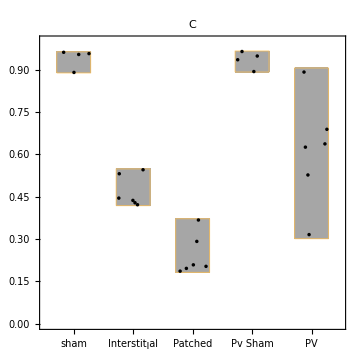
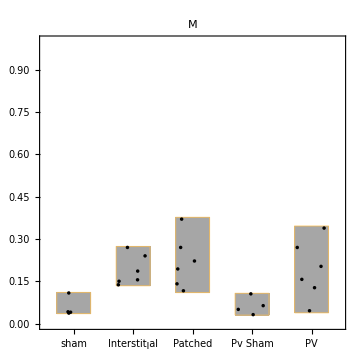
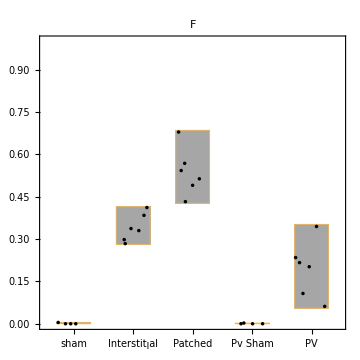
-Graphics-
 | ES | p-val
sham/Interstitןal | 0. | 0.
sham,Patched | 0. | 0.
Interstitןal/Patched | 0. | 0.
Pv Sham/Sham | 0. | 0.-Graphics-
 | ES | p-val
sham/Interstitןal | 0. | 0.
sham,Patched | 0. | 0.
Interstitןal/Patched | 16. | 0.699134
Pv Sham/Sham | 3. | 0.0380952-Graphics-
 | ES | p-val
sham/Interstitןal | 0. | 0.
sham,Patched | 0. | 0.
Interstitןal/Patched | 0. | 0.
Pv Sham/Sham | 0. | 0.

```mathematica
Row[MapIndexed[Column[{
DistributionChart[#,ChartElementFunction->"PointDensity",Frame->True,AspectRatio->1,ChartLabels->{"sham","Interstitןal","Patched","Pv Sham","PV"},ImageSize->Medium,PlotRange->{0,1},PlotLabel->{"C","M","F"}[[#2[[1]]]]],TableForm[MannWhitneyTest(*DistributionFitTest*)[#(*##*),Automatic,"TestData",Method->"Exact"(*{"TestData","KolmogorovSmirnov"}*)]&/@{#[[{1,2}]],#[[{1,3}]],#[[{2,3}]],#[[{4,5}]]},TableHeadings->{{"sham/Interstitןal","sham,Patched","Interstitןal/Patched","Pv Sham/Sham"},{"ES","p-val"}}]}]&,((Transpose/@#[[;;,2]])ᵀ)&@((Join@@(NeighborhoodCounts1PerAnimal/.x:{_Real..}:>(x/(Total@x)))[[{7,6},2]])[[{1,3,4,2,5}]])],
Spacer@10]
```

```mathematica
NeighborhoodPrecentage1=({#[[1,1,1]],{#[[1,2]],#[[2]]ᵀ}&/@#}&/@GatherBy[{#[[1,1]],#[[;;,2]]}&/@GatherBy[{#[[{2,3}]],Around[Mean@#,StandardDeviation@#]&/@(#[[4,;;,2]]ᵀ)}&/@(NCountsNoUSorted/.x:{_Integer..}:>N@(x/(Total@x)))/.rule,#[[1]]&],#[[1,1]]&]/.Around[x_,y_]:>x//N);
```

```mathematica
Row[MapIndexed[ListLinePlot[{{Callout[#[[1]],"sham"],#[[2]]},#[[2;;-2]],Callout[#[[{-1}]],"Suture",Below]}&@({{0,2,4,7,14,28,28},#}ᵀ),Frame->True,FrameTicks->{{Automatic,None},{{0,2,4,7,14,28},None}},PlotStyle->Thread[{{Dashed,None,None},{Purple,Darker@Green,Red}[[#2[[1]]]]}],PlotLabel->{"C","M","F"}[[#2[[1]]]],ImageSize->Medium,FrameLabel->{"days Post MI","Cell Count in Neighborhood"}]&,Map[Around[Mean@#,StandardDeviation@#]&,((Transpose/@Prepend[Join@@NeighborhoodCounts1PerAnimal[[{1,2,3,4,-1},2,;;-2,2]],NeighborhoodCounts1PerAnimal[[5,2,1,2]]])ᵀ),{2}]],Spacer@10]
```

-Graphics--Graphics--Graphics-

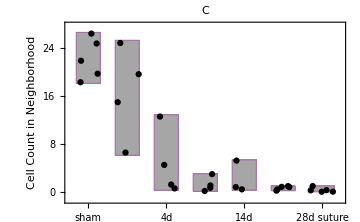
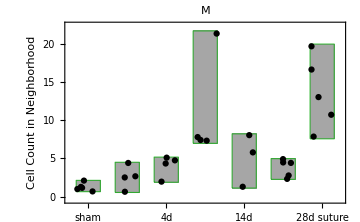
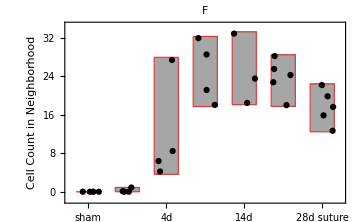

```mathematica
Row[MapIndexed[DistributionChart[#,ChartElementFunction->ChartElementData["PointDensity","PointStyle"->Directive[Black,PointSize[.0125]]],ChartLabels->{"sham","2d","4d","7d","14d","28d","28d suture"},ImageSize->Medium,FrameLabel->{None,"Cell Count in Neighborhood"},ChartStyle->{Lighter@Purple,Darker@Green,Red}[[#2[[1]]]],PlotLabel->{"C","M","F"}[[#2[[1]]]]]&,((Transpose/@Prepend[Join@@NeighborhoodCounts1PerAnimal[[{1,2,3,4,-1},2,;;-2,2]],NeighborhoodCounts1PerAnimal[[5,2,1,2]]])ᵀ)],
Spacer@10]
```

```mathematica
Row[MapIndexed[ListLinePlot[{{Callout[#[[1]],"sham"],#[[2]]},#[[2;;-2]],Callout[#[[{-1}]],"Suture",Below]}&@({{0,2,4,7,14,28,28},#}ᵀ),Frame->True,FrameTicks->{{Automatic,None},{{0,2,4,7,14,28},None}},PlotStyle->Thread[{{Dashed,None,None},{Purple,Darker@Green,Red}[[#2[[1]]]]}],PlotLabel->{"C","M","F"}[[#2[[1]]]],ImageSize->Medium,FrameLabel->{"days Post MI","% Cells in Neighborhood"}]&,Map[Around[Mean@#,StandardDeviation@#]&,((Transpose/@Prepend[Join@@NeighborhoodCounts1PerAnimalPercent[[{1,2,3,4,-1},2,;;-2,2]],NeighborhoodCounts1PerAnimalPercent[[5,2,1,2]]])ᵀ),{2}]],Spacer@10]
```

-Graphics--Graphics--Graphics-

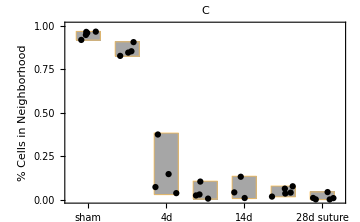
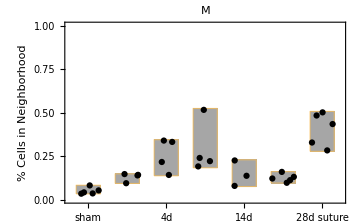
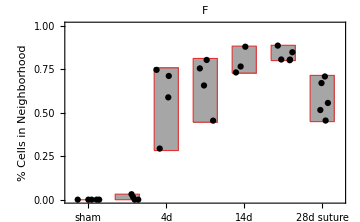

```mathematica
Row[MapIndexed[DistributionChart[#,ChartElementFunction->ChartElementData["PointDensity","PointStyle"->Directive[Black,PointSize[.0125]]],ChartLabels->{"sham","2d","4d","7d","14d","28d","28d suture"},ImageSize->Medium,FrameLabel->{None,"% Cells in Neighborhood"},ChartStyle->{Lighter@Purple,Darker@Green,Red}[[#2[[1]]]],PlotLabel->{"C","M","F"}[[#2[[1]]]],PlotRange->{0,1}]&,((Transpose/@(Prepend[Join@@NeighborhoodCounts1PerAnimalPercent[[{1,2,3,4,-1},2,;;-2,2]],NeighborhoodCounts1PerAnimalPercent[[5,2,1,2]]]))ᵀ)],
Spacer@10]
```

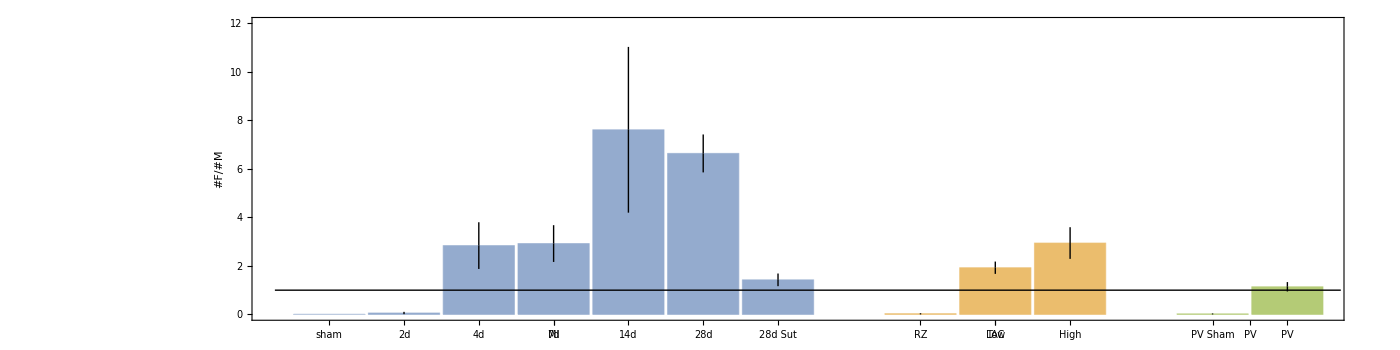

```mathematica
BarChart[
{
Labeled@@@({Prepend[MeanAround/@(Join@@NeighborhoodCounts1PerAnimal[[{1,2,3,4,-1},2,;;-2,2]]/.x:{_Real,_Real,_Real}:>x[[3]]/x[[2]]),0],{"sham","2d","4d","7d","14d","28d","28d Sut"}}ᵀ),
Labeled@@@({MeanAround/@((Join@@NeighborhoodCounts1PerAnimal[[{7,6},2]])[[{1,3,4},2]]/.x:{_Real,_Real,_Real}:>x[[3]]/x[[2]]),{"RZ","Low","High"}}ᵀ),
Labeled@@@({MeanAround/@((Join@@NeighborhoodCounts1PerAnimal[[{7,6},2]])[[{2,5},2]]/.x:{_Real,_Real,_Real}:>x[[3]]/x[[2]]),{"PV Sham","PV"}}ᵀ)},
ChartLabels->{{"MI","TAC","PV"},None},
Frame->True,FrameLabel->{Automatic,"#F/#M"},Epilog->{Thin,Line[{{.75,1},{15,1}}]},PlotRangePadding->None,ChartStyle->{Lighter/@ColorData[97]/@{1,2,3},None},AspectRatio->.25,ImageSize->1400,BarSpacing->{Tiny,1},FrameStyle->Directive[Black,14],PlotRange->{0,12}]
```

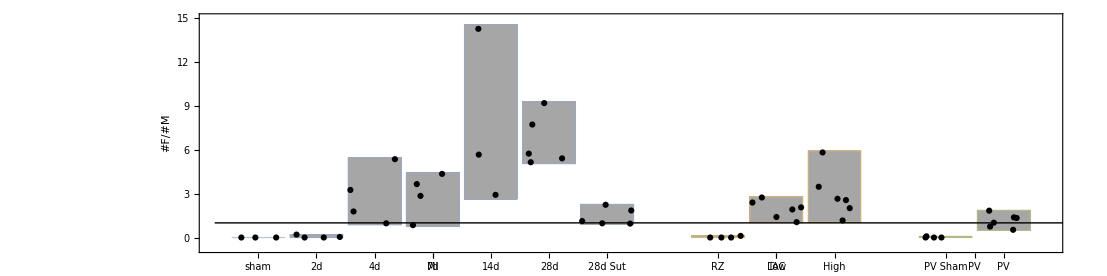

```mathematica
DistributionChart[
{
Labeled@@@({Prepend[Join@@NeighborhoodCounts1PerAnimal[[{1,2,3,4,-1},2,;;-2,2]]/.x:{_Real,_Real,_Real}:>x[[3]]/x[[2]],{0,0,0}],{"sham","2d","4d","7d","14d","28d","28d Sut"}}ᵀ),
Labeled@@@({(Join@@NeighborhoodCounts1PerAnimal[[{7,6},2]])[[{1,3,4},2]]/.x:{_Real,_Real,_Real}:>x[[3]]/x[[2]],{"RZ","Low","High"}}ᵀ),
Labeled@@@({(Join@@NeighborhoodCounts1PerAnimal[[{7,6},2]])[[{2,5},2]]/.x:{_Real,_Real,_Real}:>x[[3]]/x[[2]],{"PV Sham","PV"}}ᵀ)},
ChartLabels->{{"MI","TAC","PV"},None},
Frame->True,FrameLabel->{Automatic,"#F/#M"},Epilog->{Thin,Line[{{0.25,1},{15,1}}]},PlotRangePadding->None,
ChartElementFunction->ChartElementData["PointDensity","PointStyle"->Directive[Black,PointSize[.004]]],ChartStyle->{Lighter/@ColorData[97]/@{1,2,3},None},AspectRatio->.25,ImageSize->1400,BarSpacing->{Tiny,1},FrameStyle->Directive[Black,14]]
```

```mathematica
{TableForm[MannWhitneyTest[#,Automatic,"TestData"]&/@Thread[{#[[1]],Rest@#},List,{2}]&@(NeighborhoodCounts1PerAnimal[[{5,1,2,3,4,-1},2,1,2,;;,{3,2}]]/.x:{_Real,_Real}:>x[[1]]/x[[2]]),TableHeadings->{{"sham-2d","sham-4d","sham-7d","sham-14d","sham-28d"},{"ES","Pval"}},TableDepth->2],

TableForm[
Append[
MannWhitneyTest[#,Automatic,"TestData"]&/@Thread[{#[[3]],Delete[#,{3}]},List,{2}]&@(NeighborhoodCounts1PerAnimal[[{1,2,3,4,-1},2,1,2,;;,{3,2}]]/.x:{_Real,_Real}:>x[[1]]/x[[2]]),
MannWhitneyTest[#,Automatic,"TestData"]&@(NeighborhoodCounts1PerAnimal[[-1,2,{1,2},2]]/.x:{_Real,_Real,_Real}:>x[[2]]/x[[1]])],TableHeadings->{{"7d-2d","7d-4d","7d-14d","7d-28d","28d-28d suture"},{"ES","Pval"}}],

TableForm[
Append[
MannWhitneyTest[#,Automatic,"TestData"]&/@Subsets[((Join@@NeighborhoodCounts1PerAnimal[[{7,6},2]])[[{1,3,4},2]]/.x:{_Real,_Real,_Real}:>x[[3]]/x[[2]]),{2}],
MannWhitneyTest[#,Automatic,"TestData"]&@((Join@@NeighborhoodCounts1PerAnimal[[{7,6},2]])[[{2,5},2]]/.x:{_Real,_Real,_Real}:>x[[3]]/x[[2]])],TableHeadings->{{"sham/Interstitial","sham/Patched","Interstitial/Patched","PV/PV Sham"},{"ES","Pval"}}]}
```

{ | ES | Pval
sham-2d | 5. | 0.190476
sham-4d | 0. | 0.
sham-7d | 0. | 0.
sham-14d | 0. | 0.
sham-28d | 0. | 0., | ES | Pval
7d-2d | 0. | 0.
7d-4d | 8. | 0.885714
7d-14d | 2. | 0.114286
7d-28d | 0. | 0.
28d-28d suture | 1. | 0.00793651, | ES | Pval
sham/Interstitial | 0. | 0.
sham/Patched | 0. | 0.
Interstitial/Patched | 10. | 0.179654
PV/PV Sham | 0. | 0.}

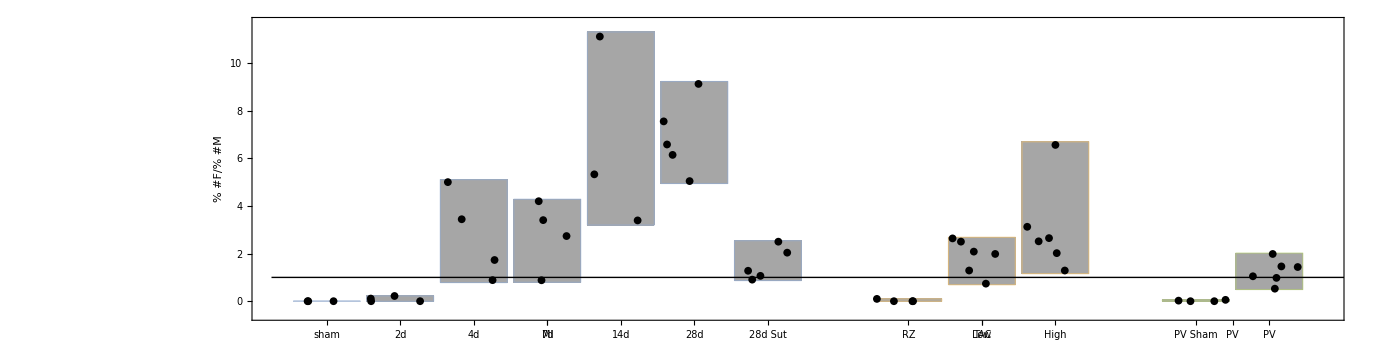

```mathematica
DistributionChart[
{
Labeled@@@({Prepend[Join@@NeighborhoodCounts1PerAnimalPercent[[{1,2,3,4,-1},2,;;-2,2]]/.x:{_Real,_Real,_Real}:>x[[3]]/x[[2]],{0,0,0}],{"sham","2d","4d","7d","14d","28d","28d Sut"}}ᵀ),
Labeled@@@({(Join@@NeighborhoodCounts1PerAnimalPercent[[{7,6},2]])[[{1,3,4},2]]/.x:{_Real,_Real,_Real}:>x[[3]]/x[[2]],{"RZ","Low","High"}}ᵀ),
Labeled@@@({(Join@@NeighborhoodCounts1PerAnimalPercent[[{7,6},2]])[[{2,5},2]]/.x:{_Real,_Real,_Real}:>x[[3]]/x[[2]],{"PV Sham","PV"}}ᵀ)},
ChartLabels->{{"MI","TAC","PV"},None},
Frame->True,FrameLabel->{Automatic,"% #F/% #M"},Epilog->{Thin,Line[{{0.25,1},{15,1}}]},PlotRangePadding->None,
ChartElementFunction->ChartElementData["PointDensity","PointStyle"->Directive[Black,PointSize[.004]]],ChartStyle->{Lighter/@ColorData[97]/@{1,2,3},None},AspectRatio->.25,ImageSize->1400,BarSpacing->{Tiny,1},FrameStyle->Directive[Black,14]]
```

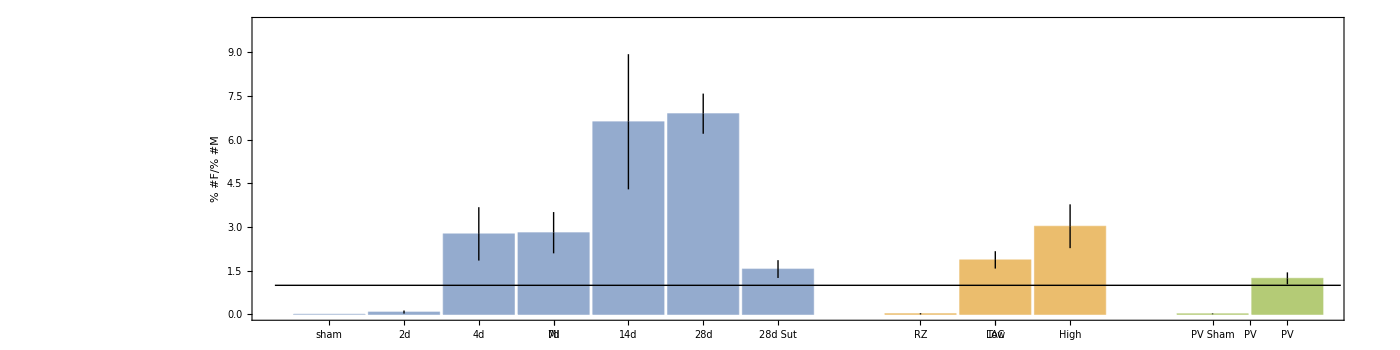

```mathematica
BarChart[
{
Labeled@@@({Prepend[MeanAround/@(Join@@NeighborhoodCounts1PerAnimalPercent[[{1,2,3,4,-1},2,;;-2,2]]/.x:{_Real,_Real,_Real}:>x[[3]]/x[[2]]),0],{"sham","2d","4d","7d","14d","28d","28d Sut"}}ᵀ),
Labeled@@@({MeanAround/@((Join@@NeighborhoodCounts1PerAnimalPercent[[{7,6},2]])[[{1,3,4},2]]/.x:{_Real,_Real,_Real}:>x[[3]]/x[[2]]),{"RZ","Low","High"}}ᵀ),
Labeled@@@({MeanAround/@((Join@@NeighborhoodCounts1PerAnimalPercent[[{7,6},2]])[[{2,5},2]]/.x:{_Real,_Real,_Real}:>x[[3]]/x[[2]]),{"PV Sham","PV"}}ᵀ)},
ChartLabels->{{"MI","TAC","PV"},None},
Frame->True,FrameLabel->{Automatic,"% #F/% #M"},Epilog->{Thin,Line[{{.75,1},{15,1}}]},PlotRangePadding->None,ChartStyle->{Lighter/@ColorData[97]/@{1,2,3},None},AspectRatio->.25,ImageSize->1400,BarSpacing->{Tiny,1},FrameStyle->Directive[Black,14],PlotRange->{0,10}]
```

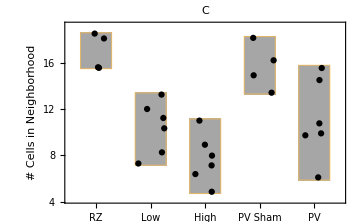
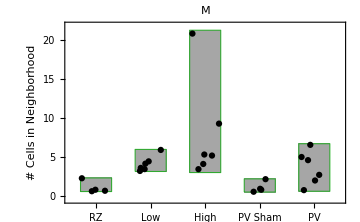
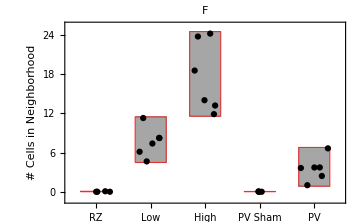

```mathematica
Row[
MapIndexed[
DistributionChart[#,ChartElementFunction->ChartElementData["PointDensity","PointStyle"->Directive[Black,PointSize[.0125]]],ChartLabels->{"RZ","Low","High","PV Sham","PV"},ImageSize->Medium,FrameLabel->{None,"# Cells in Neighborhood"},ChartStyle->{Lighter@Purple,Darker@Green,Red}[[#2[[1]]]],PlotLabel->{"C","M","F"}[[#2[[1]]]]]&,((Transpose/@Join[
(Join@@NeighborhoodCounts1PerAnimal[[{7,6},2]])[[{1,3,4},2]],
(Join@@NeighborhoodCounts1PerAnimal[[{7,6},2]])[[{2,5},2]]])ᵀ)],
Spacer@10]
```

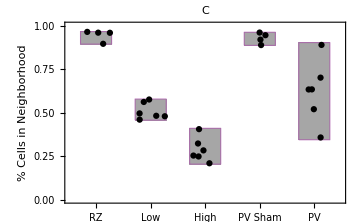
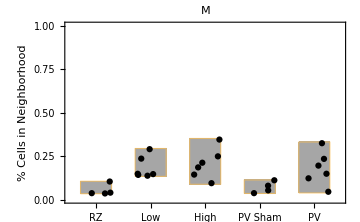
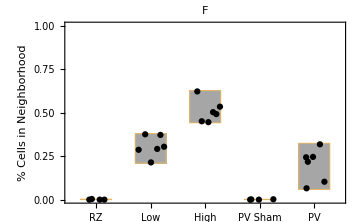

```mathematica
Row[
MapIndexed[
DistributionChart[#,ChartElementFunction->ChartElementData["PointDensity","PointStyle"->Directive[Black,PointSize[.0125]]],ChartLabels->{"RZ","Low","High","PV Sham","PV"},ImageSize->Medium,FrameLabel->{None,"% Cells in Neighborhood"},ChartStyle->{Lighter@Purple,Darker@Green,Red}[[#2[[1]]]],PlotLabel->{"C","M","F"}[[#2[[1]]]],PlotRange->{0,1}]&,((Transpose/@Join[
(Join@@NeighborhoodCounts1PerAnimalPercent[[{7,6},2]])[[{1,3,4},2]],
(Join@@NeighborhoodCounts1PerAnimalPercent[[{7,6},2]])[[{2,5},2]]])ᵀ)],
Spacer@10]
```

```mathematica
Row[
MapIndexed[
ListLinePlot[{#[[1]],{#[[4,1]],#[[1,1]]},#[[3]]},PlotStyle->{{Purple,Darker@Green,Red}[[#2[[1]]]],{Dashed,{Purple,Darker@Green,Red}[[#2[[1]]]]},{Purple,Darker@Green,Red}[[#2[[1]]]]},Frame->True,Axes->False,ImageSize->Medium,FrameTicks->{{Automatic,None},{{(*{0,"sham"},*)2,4,7,14,28},None}},FrameLabel->{"time (days)","Neighborhood Cell Count"},PlotLabel->{"C","M","F"}[[#2[[1]]]],PlotRange->{{-.1,30},All}]&,Join[{{2,4,7,14,28},#}ᵀ&/@#[[;;2]],{{Callout[{28,#[[3]]},"Suture",LabelVisibility->All]},{Callout[{0,#[[4]]},"sham",LabelVisibility->All]}}]&/@(Join@@@({((Transpose/@(NeighborhoodCounts[[{1,2,3,4,-1},2,{1,-1},2]]ᵀ))ᵀ),{#}&/@NeighborhoodCounts[[-1,2,2,2]],{#}&/@NeighborhoodCounts[[5,2,1,2]]}ᵀ))],

Spacer@10]
```

-Graphics--Graphics--Graphics-

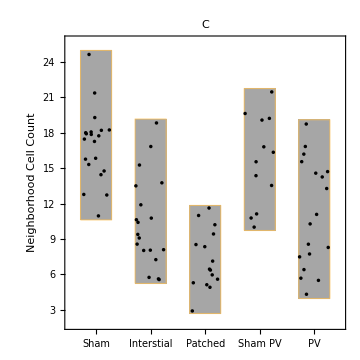
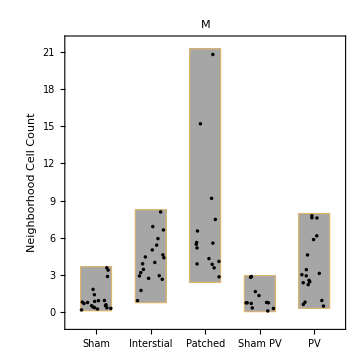
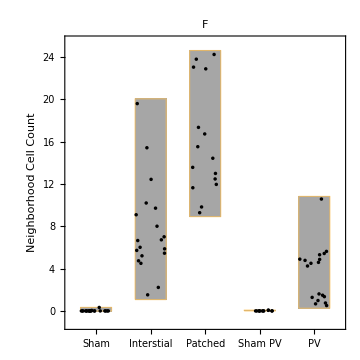
-Graphics-
 | ES | P-val
Interstial/Sham | 0.692105 | 0.0000649299
Patched/Sham | 0.95 | 9.85239×10^-9
Interstial/Patched | 0.442105 | 0.0537421
PV/PV sham | 0.444444 | 0.0945069-Graphics-
 | ES | P-val
Interstial/Sham | 0.747368 | 5.82544×10^-6
Patched/Sham | 0.883333 | 2.50004×10^-7
Interstial/Patched | 0.354386 | 0.182425
PV/PV sham | 0.611111 | 0.00571275-Graphics-
 | ES | P-val
Interstial/Sham | 1 | 2.90178×10^-11
Patched/Sham | 1 | 3.07887×10^-10
Interstial/Patched | 0.736842 | 0.0000552531
PV/PV sham | 1 | 2.31232×10^-8

```mathematica
Row[MapIndexed[
Column[{
DistributionChart[{#[[1]],#[[3]],#[[4]],#[[2]],#[[5]]},ChartElementFunction->"PointDensity",ChartLabels->{"Sham","Interstial","Patched","Sham\nPV","PV"},ImageSize->Medium,AspectRatio->1,PlotLabel->{"C","M","F"}[[#2[[1]]]],FrameLabel->{Automatic,"Neighborhood Cell Count"}],
TableForm[KolmogorovSmirnovTest[#[[1]],#[[2]],(*Automatic,*)"TestData"]&/@{#[[{1,3}]],#[[{4,1}]],#[[{3,4}]],#[[{5,2}]]},TableHeadings->{{"Interstial/Sham","Patched/Sham","Interstial/Patched","PV/PV sham"},{"ES","P-val"}}]}]&,
(Join@@@({NeighborhoodCounts1[[7,2,;;,2]]ᵀ,NeighborhoodCounts1[[6,2,;;,2]]ᵀ}ᵀ))],Spacer@10]
```

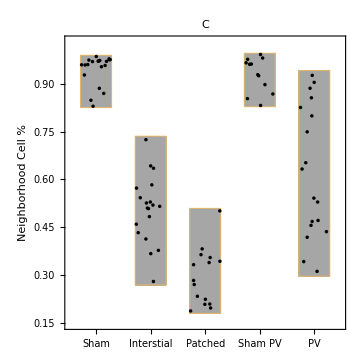
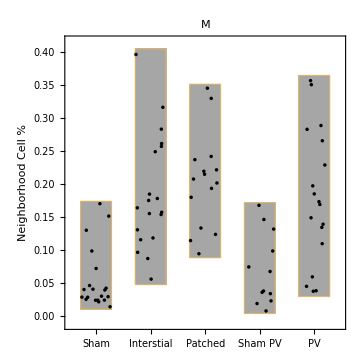
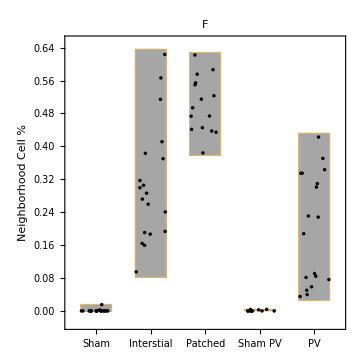
-Graphics-
 | ES | P-val
Interstial/Sham | 1 | 2.90178×10^-11
Patched/Sham | 1 | 6.15774×10^-10
Interstial/Patched | 0.814035 | 5.24147×10^-6
PV/PV sham | 0.777778 | 0.000101164-Graphics-
 | ES | P-val
Interstial/Sham | 0.75 | 3.31177×10^-6
Patched/Sham | 0.8 | 5.8203×10^-6
Interstial/Patched | 0.364912 | 0.161258
PV/PV sham | 0.555556 | 0.0162856-Graphics-
 | ES | P-val
Interstial/Sham | 1 | 2.90178×10^-11
Patched/Sham | 1 | 3.07887×10^-10
Interstial/Patched | 0.789474 | 9.58099×10^-6
PV/PV sham | 1 | 2.31232×10^-8

```mathematica
Row[MapIndexed[
Column[{
DistributionChart[{#[[1]],#[[3]],#[[4]],#[[2]],#[[5]]},ChartElementFunction->"PointDensity",ChartLabels->{"Sham","Interstial","Patched","Sham\nPV","PV"},ImageSize->Medium,AspectRatio->1,PlotLabel->{"C","M","F"}[[#2[[1]]]],FrameLabel->{Automatic,"Neighborhood Cell %"}],
TableForm[KolmogorovSmirnovTest[#[[1]],#[[2]],(*Automatic,*)"TestData"]&/@{#[[{1,3}]],#[[{4,1}]],#[[{3,4}]],#[[{5,2}]]},TableHeadings->{{"Interstial/Sham","Patched/Sham","Interstial/Patched","PV/PV sham"},{"ES","P-val"}}]}]&,
(Join@@@({NeighborhoodPrecentage1[[7,2,;;,2]]ᵀ,NeighborhoodPrecentage1[[6,2,;;,2]]ᵀ}ᵀ))],Spacer@10]
```

counts all vs day 7

```mathematica
TableForm[Join[
(KolmogorovSmirnovTest[#[[1]],#[[2]],"TestData"]&/@Thread[#,List,{1}]&/@(
{
NeighborhoodCounts1[[{1,2,4},2,1,2]]ᵀ,
NeighborhoodCounts1[[3,2,1,2]]
}ᵀ))ᵀ,
(KolmogorovSmirnovTest[#[[1]],#[[2]],"TestData"]&/@Thread[#,List,{1}]&/@(
{
NeighborhoodCounts1[[-1,2,{1,2},2]]ᵀ,
NeighborhoodCounts1[[3,2,1,2]]
}ᵀ))ᵀ
],
TableHeadings->{{"2d:IZ~7d:IZ","4d:IZ~7d:IZ","14d:IZ-7d:IZ","28d:IZ~7d:IZ","28d:suture~7d:IZ","28d:IZ~suture~7d:IZ"},{"C","M","F"}},TableDepth->2]
```

| C | M | F
2d:IZ~7d:IZ | {0.9,0.0000680434} | {0.8,0.000714456} | {1,3.09288×10^-6}
4d:IZ~7d:IZ | {0.233333,0.863089} | {0.633333,0.0153067} | {0.75,0.00135778}
14d:IZ-7d:IZ | {0.3,0.722748} | {0.55,0.095114} | {0.275,0.822707}
28d:IZ~7d:IZ | {0.264706,0.668086} | {0.623529,0.00822756} | {0.235294,0.789807}
28d:suture~7d:IZ | {0.5,0.167821} | {0.4,0.417524} | {0.5,0.167821}

counts all vs remote zone

```mathematica
TableForm[

Join[
Map[KolmogorovSmirnovTest[#[[1]],#[[2]],"TestData"]&,(Transpose/@(NeighborhoodCounts1)[[{1,2,3,4},2,{1,-1},2]]),{2}],

Map[KolmogorovSmirnovTest[#[[1]],#[[2]],"TestData"]&,Subsets[#,{2}][[{2,3,1}]]&/@Transpose[NeighborhoodCounts1[[-1,2,;;,2]]],{2}]],


TableDepth->2,TableHeadings->{{"2d:IZ~RZ","4d:IZ~RZ","7d:IZ~RZ","14d:IZ-RZ","28d:IZ~RZ","28d:suture~RZ","28d:IZ~suture"},{"C","M","F"}}]
```

| C | M | F
2d:IZ~RZ | {0.5,0.0995468} | {0.666667,0.00785901} | {0.5,0.01373}
4d:IZ~RZ | {0.833333,0.00020413} | {0.75,0.00149696} | {0.833333,0.00020413}
7d:IZ~RZ | {0.9,0.000216502} | {0.9,0.000216502} | {0.9,0.000216502}
14d:IZ-RZ | {1,0.0000822707} | {0.875,0.0013986} | {1,0.0000411353}
28d:IZ~RZ | {1,2.91395×10^-12} | {1,5.74168×10^-9} | {0.523529,0.0436322}
28d:suture~RZ | {0.638344,0.00016066} | {1,5.74168×10^-9} | {0.664706,0.00385644}
28d:IZ~suture | {1,1.45697×10^-12} | {1,2.87084×10^-9} | {0.329412,0.399405}

counts all vs sham

```mathematica
{TableForm[(MannWhitneyTest[#,Automatic,"TestData"]&/@Thread[#,List,{1}]&/@({
(Transpose/@(Join@@NeighborhoodCounts1PerAnimal[[{1,2,3,4,-1},2,;;-2,2]]))ᵀ,
NeighborhoodCounts1PerAnimal[[5,2,1,2]]ᵀ
}ᵀ))ᵀ,
TableHeadings->{{"2d:IZ~sham","4d:IZ~sham","7d:IZ~sham","14d:IZ-sham","28d:IZ~sham","28d:suture~sham","28d:IZ~suture"},{"C","M","F"}},TableDepth->2],

TableForm[(MannWhitneyTest[#,Automatic,"TestData"]&/@
Thread[#,List,{1}]&/@({
(Transpose/@(Join@@NeighborhoodCounts1PerAnimal[[{1,2,4,-1},2,;;-2,2]]))ᵀ,
NeighborhoodCounts1PerAnimal[[3,2,1,2]]ᵀ
}ᵀ))ᵀ,
TableHeadings->{{"2d:IZ~7d:IZ","4d:IZ~7d:IZ","14d:IZ-7d:IZ","28d:IZ~7d:IZ","28d:suture~7d:IZ"},{"C","M","F"}},TableDepth->2],

TableForm[Map[MannWhitneyTest[#,Automatic,"TestData"]&,Transpose/@Map[Transpose,Partition[(Join@@NeighborhoodCounts1PerAnimal[[{7,6},2]])[[{1,3,1,4,3,4,2,5},2]],2],{2}],{2}],TableDepth->2,TableHeadings->{{"RZ~Low","RZ~High","Low~High","PV Sham~PV"},{"C","M","F"}}]}
```

{ | C | M | F
2d:IZ~sham | {5.,0.190476} | {5.,0.190476} | {5.,0.190476}
4d:IZ~sham | {0.,0.} | {1.,0.015873} | {0.,0.}
7d:IZ~sham | {0.,0.} | {0.,0.} | {0.,0.}
14d:IZ-sham | {0.,0.} | {1.,0.0357143} | {0.,0.}
28d:IZ~sham | {0.,0.} | {0.,0.} | {0.,0.}
28d:suture~sham | {0.,0.} | {0.,0.} | {0.,0.}, | C | M | F
2d:IZ~7d:IZ | {0.,0.} | {0.,0.} | {0.,0.}
4d:IZ~7d:IZ | {4.,0.2} | {0.,0.} | {2.,0.0571429}
14d:IZ-7d:IZ | {5.,0.628571} | {3.,0.228571} | {5.,0.628571}
28d:IZ~7d:IZ | {8.,0.555556} | {0.,0.} | {8.,0.555556}
28d:suture~7d:IZ | {4.,0.111111} | {5.,0.190476} | {3.,0.0634921}, | C | M | F
RZ~Low | {0.,0.} | {0.,0.} | {0.,0.}
RZ~High | {0.,0.} | {0.,0.} | {0.,0.}
Low~High | {6.,0.0411255} | {10.,0.179654} | {0.,0.}
PV Sham~PV | {3.,0.0380952} | {4.,0.0666667} | {0.,0.}}

```mathematica
MannWhitneyTest[#,Automatic,"TestData"]&/@((Transpose/@NeighborhoodCounts1PerAnimal[[8,2,;;2,2]])ᵀ)
```

{{7.,0.222222},{0.,0.},{2.,0.015873}}

```mathematica
{TableForm[(MannWhitneyTest[#,Automatic,"TestData"]&/@Thread[#,List,{1}]&/@({
(Transpose/@(Join@@NeighborhoodCounts1PerAnimalPercent[[{1,2,3,4,-1},2,;;-2,2]]))ᵀ,
NeighborhoodCounts1PerAnimalPercent[[5,2,1,2]]ᵀ
}ᵀ))ᵀ,
TableHeadings->{{"2d:IZ~sham","4d:IZ~sham","7d:IZ~sham","14d:IZ-sham","28d:IZ~sham","28d:suture~sham","28d:IZ~suture"},{"C","M","F"}},TableDepth->2],
TableForm[(MannWhitneyTest[#,Automatic,"TestData"]&/@Thread[#,List,{1}]&/@({
(Transpose/@(Join@@NeighborhoodCounts1PerAnimalPercent[[{1,2,4,-1},2,;;-2,2]]))ᵀ,
NeighborhoodCounts1PerAnimalPercent[[3,2,1,2]]ᵀ
}ᵀ))ᵀ,
TableHeadings->{{"2d:IZ~7d:IZ","4d:IZ~7d:IZ","14d:IZ-7d:IZ","28d:IZ~7d:IZ","28d:suture~7d:IZ"},{"C","M","F"}},TableDepth->2],
TableForm[Map[MannWhitneyTest[#,Automatic,"TestData"]&,Transpose/@Map[Transpose,Partition[(Join@@NeighborhoodCounts1PerAnimalPercent[[{7,6},2]])[[{1,3,1,4,3,4,2,5},2]],2],{2}],{2}],TableDepth->2,TableHeadings->{{"RZ~Low","RZ~High","Low~High","PV Sham~PV"},{"C","M","F"}}]}
```

{ | C | M | F
2d:IZ~sham | {0.,0.} | {0.,0.} | {5.,0.190476}
4d:IZ~sham | {0.,0.} | {0.,0.} | {0.,0.}
7d:IZ~sham | {0.,0.} | {0.,0.} | {0.,0.}
14d:IZ-sham | {0.,0.} | {1.,0.0357143} | {0.,0.}
28d:IZ~sham | {0.,0.} | {0.,0.} | {0.,0.}
28d:suture~sham | {0.,0.} | {0.,0.} | {0.,0.}, | C | M | F
2d:IZ~7d:IZ | {0.,0.} | {0.,0.} | {0.,0.}
4d:IZ~7d:IZ | {2.,0.0571429} | {7.,0.685714} | {5.,0.342857}
14d:IZ-7d:IZ | {4.,0.4} | {2.,0.114286} | {3.,0.228571}
28d:IZ~7d:IZ | {7.,0.412698} | {0.,0.} | {1.,0.015873}
28d:suture~7d:IZ | {5.,0.190476} | {5.,0.190476} | {7.,0.412698}, | C | M | F
RZ~Low | {0.,0.} | {0.,0.} | {0.,0.}
RZ~High | {0.,0.} | {1.,0.00952381} | {0.,0.}
Low~High | {0.,0.} | {15.,0.588745} | {0.,0.}
PV Sham~PV | {1.,0.00952381} | {3.,0.0380952} | {0.,0.}}

```mathematica
MannWhitneyTest[#,Automatic,"TestData"]&/@((Transpose/@NeighborhoodCounts1PerAnimalPercent[[8,2,;;2,2]])ᵀ)
```

{{3.,0.031746},{0.,0.},{0.,0.}}

```mathematica
NeighborhoodPercents={#[[1,1,1]],{#[[1,2]],#[[2]]}&/@#}&/@GatherBy[{#[[1,1]],Mean@#[[;;,2]]}&/@GatherBy[{#[[{2,3}]],Around[Mean@#,StandardDeviation@#]&/@(#[[4,;;,2]]ᵀ)}&/@(NCountsNoUSorted/.x:{_Integer..}:>N@(x/(Total@x)))/.rule,#[[1]]&],#[[1,1]]&];
```

```mathematica
Row[
MapIndexed[
ListLinePlot[{#[[1]],{#[[4,1]],#[[1,1]]},#[[3]]},PlotStyle->{{Purple,Darker@Green,Red}[[#2[[1]]]],{Dashed,{Purple,Darker@Green,Red}[[#2[[1]]]]},{Purple,Darker@Green,Red}[[#2[[1]]]]},Frame->True,Axes->False,ImageSize->Medium,FrameTicks->{{Automatic,None},{{(*{0,"sham"},*)2,4,7,14,28},None}},FrameLabel->{"time (days)","Neighborhood Cell %"},PlotLabel->{"C","M","F"}[[#2[[1]]]],PlotRange->{{-.1,30},All}]&,Join[{{2,4,7,14,28},#}ᵀ&/@#[[;;2]],{{Callout[{28,#[[3]]},"Suture",LabelVisibility->All]},{Callout[{0,#[[4]]},"sham",LabelVisibility->All]}}]&/@(Join@@@({((Transpose/@(NeighborhoodPercents[[{1,2,3,4,-1},2,{1,-1},2]]ᵀ))ᵀ),{#}&/@NeighborhoodPercents[[-1,2,2,2]],{#}&/@NeighborhoodPercents[[5,2,1,2]]}ᵀ))],

Spacer@10]
```

-Graphics--Graphics--Graphics-

% all vs day 7

```mathematica
TableForm[Join[
(KolmogorovSmirnovTest[#[[1]],#[[2]],"TestData"]&/@Thread[#,List,{1}]&/@(
{
NeighborhoodPrecentage1[[{1,2,4},2,1,2]]ᵀ,
NeighborhoodPrecentage1[[3,2,1,2]]
}ᵀ))ᵀ,
(KolmogorovSmirnovTest[#[[1]],#[[2]],"TestData"]&/@Thread[#,List,{1}]&/@(
{
NeighborhoodPrecentage1[[-1,2,{1,2},2]]ᵀ,
NeighborhoodPrecentage1[[3,2,1,2]]
}ᵀ))ᵀ
],
TableHeadings->{{"2d:IZ~7d:IZ","4d:IZ~7d:IZ","14d:IZ-7d:IZ","28d:IZ~7d:IZ","28d:suture~7d:IZ","28d:IZ~suture~7d:IZ"},{"C","M","F"}},TableDepth->2]
```

| C | M | F
2d:IZ~7d:IZ | {1,3.09288×10^-6} | {0.716667,0.00391868} | {1,3.09288×10^-6}
4d:IZ~7d:IZ | {0.4,0.282949} | {0.233333,0.863089} | {0.283333,0.671282}
14d:IZ-7d:IZ | {0.275,0.822707} | {0.675,0.0206591} | {0.45,0.247543}
28d:IZ~7d:IZ | {0.205882,0.888568} | {0.8,0.000132523} | {0.623529,0.00822756}
28d:suture~7d:IZ | {0.5,0.167821} | {0.4,0.417524} | {0.3,0.78693}

% all vs remote zone

```mathematica
TableForm[

Join[
Map[KolmogorovSmirnovTest[#[[1]],#[[2]],"TestData"]&,(Transpose/@(NeighborhoodPrecentage1)[[{1,2,3,4},2,{1,-1},2]]),{2}],

Map[KolmogorovSmirnovTest[#[[1]],#[[2]],"TestData"]&,Subsets[#,{2}][[{2,3,1}]]&/@Transpose[NeighborhoodPrecentage1[[-1,2,;;,2]]],{2}]],


TableDepth->2,TableHeadings->{{"2d:IZ~RZ","4d:IZ~RZ","7d:IZ~RZ","14d:IZ-RZ","28d:IZ~RZ","28d:suture~RZ","28d:IZ~suture"},{"C","M","F"}}]
```

| C | M | F
2d:IZ~RZ | {0.833333,0.00020413} | {0.833333,0.00020413} | {0.5,0.01373}
4d:IZ~RZ | {0.833333,0.00020413} | {0.833333,0.00020413} | {0.833333,0.00020413}
7d:IZ~RZ | {0.9,0.000216502} | {0.9,0.000216502} | {0.9,0.000216502}
14d:IZ-RZ | {1,0.0000822707} | {0.763889,0.00830934} | {1,0.0000411353}
28d:IZ~RZ | {1,2.91395×10^-12} | {1,5.74168×10^-9} | {0.582353,0.0173105}
28d:suture~RZ | {0.653595,0.0000967561} | {1,5.74168×10^-9} | {0.9,6.40092×10^-6}
28d:IZ~suture | {1,1.45697×10^-12} | {1,2.87084×10^-9} | {0.782353,0.000278559}

% all vs sham

```mathematica
TableForm[Join[
(KolmogorovSmirnovTest[#[[1]],#[[2]],"TestData"]&/@Thread[#,List,{1}]&/@(
{
NeighborhoodPrecentage1[[{1,2,3,4},2,1,2]]ᵀ,
NeighborhoodPrecentage1[[5,2,1,2]]
}ᵀ))ᵀ,
(KolmogorovSmirnovTest[#[[1]],#[[2]],"TestData"]&/@Thread[#,List,{1}]&/@(
{
NeighborhoodPrecentage1[[-1,2,;;2,2]]ᵀ,
NeighborhoodPrecentage1[[5,2,1,2]]
}ᵀ))ᵀ
],
TableHeadings->{{"2d:IZ~sham","4d:IZ~sham","7d:IZ~sham","14d:IZ-sham","28d:IZ~sham","28d:suture~sham","28d:IZ~suture"},{"C","M","F"}},TableDepth->2]
```

| C | M | F
2d:IZ~sham | {0.833333,0.00409395} | {0.833333,0.00409395} | {0.5,0.118886}
4d:IZ~sham | {0.916667,0.000754148} | {0.916667,0.000754148} | {0.916667,0.000754148}
7d:IZ~sham | {1,0.00024975} | {1,0.00024975} | {1,0.00024975}
14d:IZ-sham | {1,0.000666001} | {0.875,0.004662} | {1,0.000666001}
28d:IZ~sham | {1,0.0000198124} | {0.823529,0.00194161} | {1,0.0000198124}
28d:suture~sham | {1,0.00024975} | {1,0.00024975} | {1,0.00024975}

```mathematica
Fractions={#[[1,;;2]],Sort[{#[[1,1]],MeanAround/@((N@((#[[;;2]])/(Total@#))&/@#[[;;,2]])ᵀ)}&/@GatherBy[#[[;;,3;;]],#[[1]]&]]}&/@GatherBy[({Sequence@@#[[;;3]],Table[Count[#[[4,;;,1]],c],{c,{"F","M","C"(*,"U"*)}}]}&/@NCounts)/.{
x_?(Quiet@StringContainsQ[#,"Fibrosis"]&):>StringSplit[x," "][[1]],
x_?(Quiet@StringContainsQ[#,"RZ"]&):>StringTake[x,2],
x_?(Quiet@StringContainsQ[#,"IZ"]&):>StringTake[x,2],
x_?(Quiet@StringContainsQ[#,"PV Sham"]&):>StringTake[x,7],
x_?(Quiet@StringContainsQ[#,"Suture"]&):>"Suture"},#[[;;2]]&];
```

```mathematica
Time={#[[1,1,2]],{#[[1,1]],#[[;;,2]]}&/@GatherBy[Join@@#[[;;,2]],First]}&/@GatherBy[Fractions,#[[1,2]]&];
```

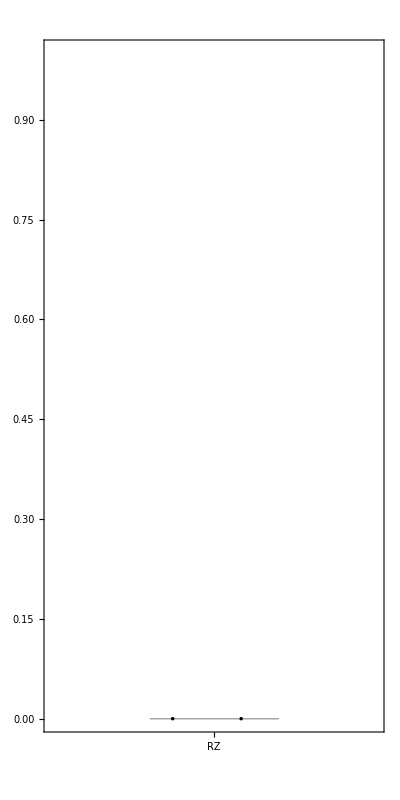
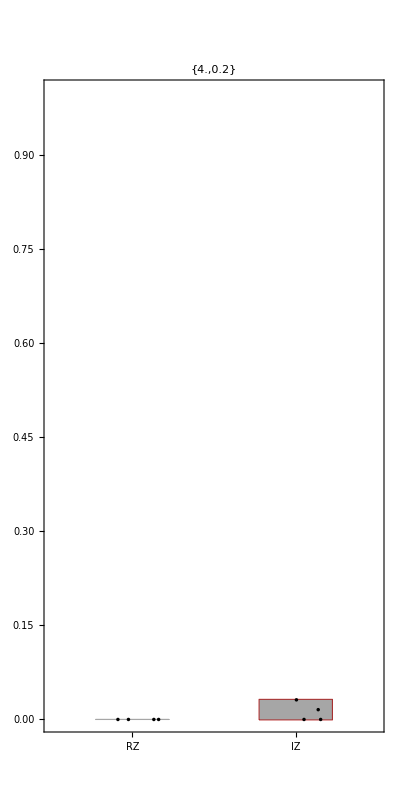
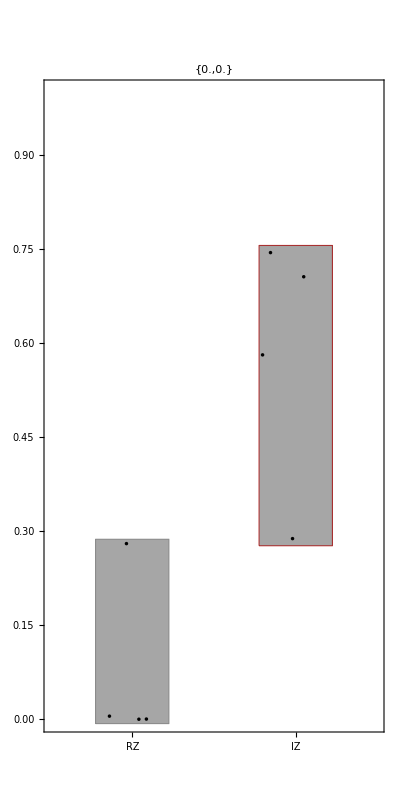
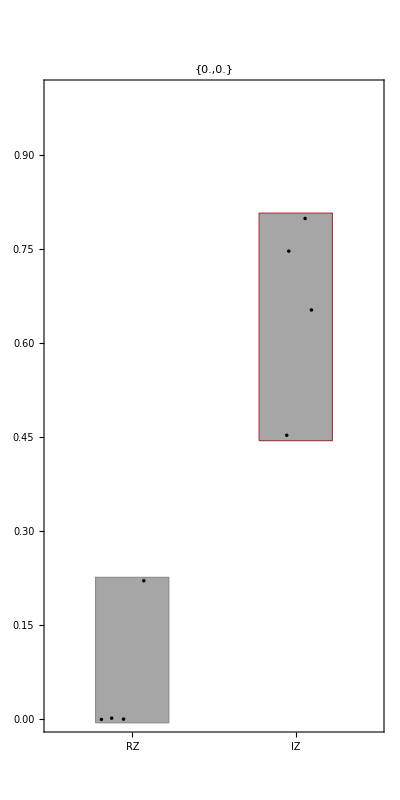
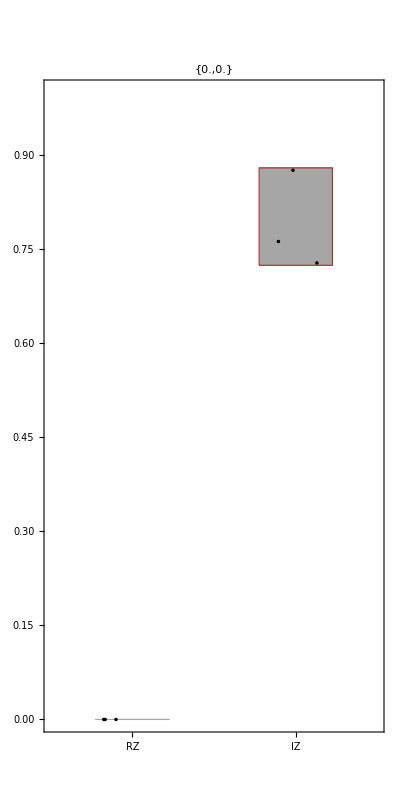
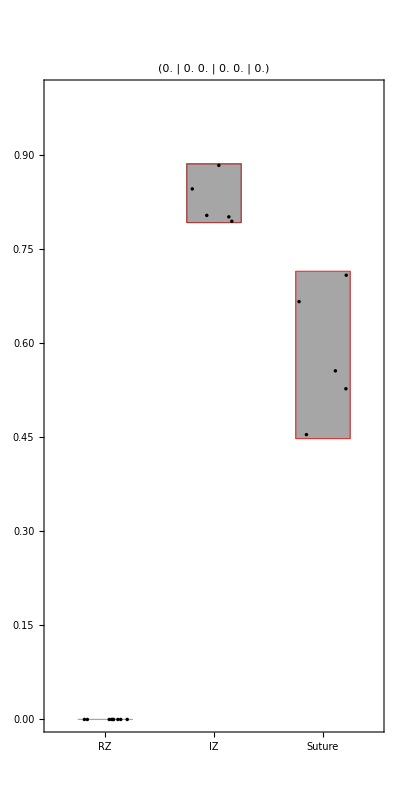
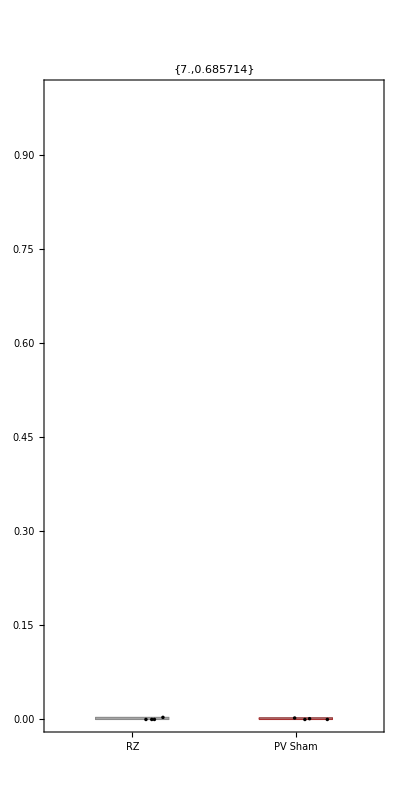
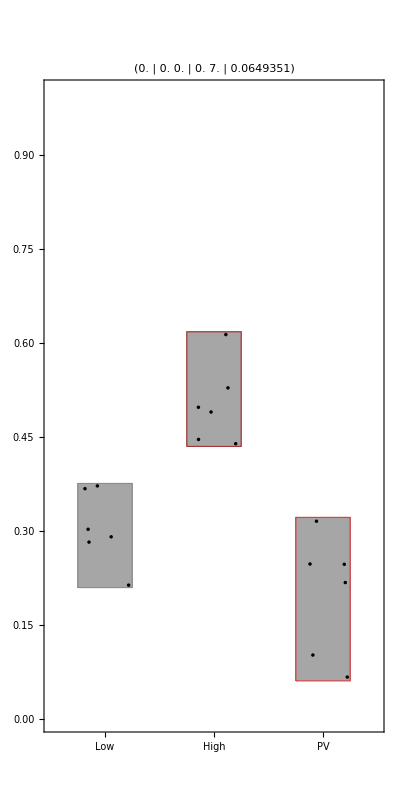
| sham | 2d | 4d | 7d | 14d | 28d | SHAM | TAC
%F | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
%M | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[
{DistributionChart[
If[Length@#>1,Prepend[Delete[#,{2}],#[[2]]],#]&@(#[[2,;;,2,;;,1]]),
ChartStyle->{Gray,Darker@Red,Red},
ChartLabels->{None,If[Length@#>1,Prepend[Delete[#,{2}],#[[2]]],#]&@#[[2,;;,1]]},
PlotLabel->Which[
Length@#[[2]]==2,MannWhitneyTest[#[[2,;;,2,;;,1]],Automatic,"TestData"],
Length@#[[2]]==3,(MannWhitneyTest[#,Automatic,"TestData"]&/@Subsets[#[[2,;;,2,;;,1]],{2}]) ,
True,""],
ChartElementFunction->"PointDensity",PlotRange->{{0.5,Length@#[[2]]+.5},{0,1}},AspectRatio->2]&/@(Time[[{5,1,2,3,4,-1,7,6}]]/.Around[x_,y_]:>x),
DistributionChart[
If[Length@#>1,Prepend[Delete[#,{2}],#[[2]]],#]&@(#[[2,;;,2,;;,2]]),
PlotLabel->Which[
Length@#[[2]]==2,MannWhitneyTest[#[[2,;;,2,;;,1]],Automatic,"TestData"],
Length@#[[2]]==3,(MannWhitneyTest[#,Automatic,"TestData"]&/@Subsets[#[[2,;;,2,;;,1]],{2}]) ,
True,""],
ChartStyle->{Gray,Darker@Green,Green},
ChartLabels->({None,If[Length@#>1,Prepend[Delete[#,{2}],#[[2]]],#]&@#[[2,;;,1]]}),ChartElementFunction->"PointDensity",PlotRange->{0,1},AspectRatio->2]&/@(Time[[{5,1,2,3,4,-1,7,6}]]/.Around[x_,y_]:>x)},
TableHeadings->{{"%F","%M"},Time[[{5,1,2,3,4,-1,7,6},1]]},TableAlignments->{Center, Center}]
```

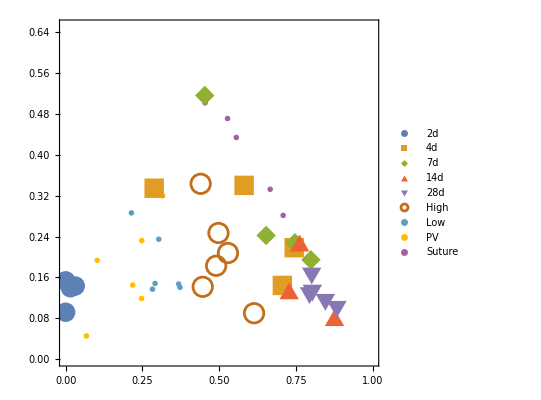

```mathematica
ListPlot[Tooltip@@@#/.Around[x_,y_]:>x,PlotLegends->#[[;;,2]],AspectRatio->1,Frame->True,PlotRange->{{0,1},{0,.65}},PlotMarkers->{Automatic,20}]&@Join[{#[[2,1,2]],#[[1]]}&/@Time[[{1,2,3,4,8}]],Reverse/@Time[[6,2]],Reverse/@Time[[8,2,{-1}]]]
```

```mathematica
Show[{
ListPlot[{Tooltip[Mean@#[[1]],#[[2]]]}&/@#,PlotLegends->#[[;;,2]],AspectRatio->1,Frame->True,PlotRange->{{0,1},{0,.5}},PlotMarkers->{Automatic,20},FrameLabel->{"%F","%M"}]&@Join[{#[[2,1,2]],#[[1]]}&/@Time[[{1,2,3,4,8}]],Reverse/@Time[[6,2]],Reverse/@Time[[8,2,{-1}]]],
ListLinePlot[
Join[
Mean/@Map[Mean,GatherBy[Cases[Time,{"RZ"|"PV Sham",x_},∞],First][[;;,;;,2]],{2}],
(Mean@#[[1]]&/@#)[[;;,;;,1]]],
PlotStyle->{{Thin,Black}}]&@({#[[2,1,2]],#[[1]]}&/@Time[[{1,2,3,4,8}]]),
ListLinePlot[Mean/@Time[[6,2,;;,2]],PlotStyle->{{Thin,Red}}],
ListPlot[Callout@@@((Reverse/@{
{"sham MI",#[[5,2,1,2]]},
{"remote MI",First@Median@(#[[{1,2,3,4,-1},2,;;,2]]/.Around[x_,_]:>x)(*First@Mean@#[[{1,2,3,4,-1},2,;;,2]]*)},
{"sham TAC interstitial",#[[6,2,1,2]]},
{"sham TAC PV",#[[6,2,2,2]]}})&@({#[[1]],{#[[1]],Mean@#[[2]]}&/@#[[2]]}&/@DeleteCases[{#[[1]],ReverseSort@Cases[#[[2]],{"RZ"|"PV Sham",_}]}&/@Time,{_,{}}])),AspectRatio->1,PlotRange->All,Frame->True,PlotStyle->Black],
ImageSize->Large}]
```

-Graphics-

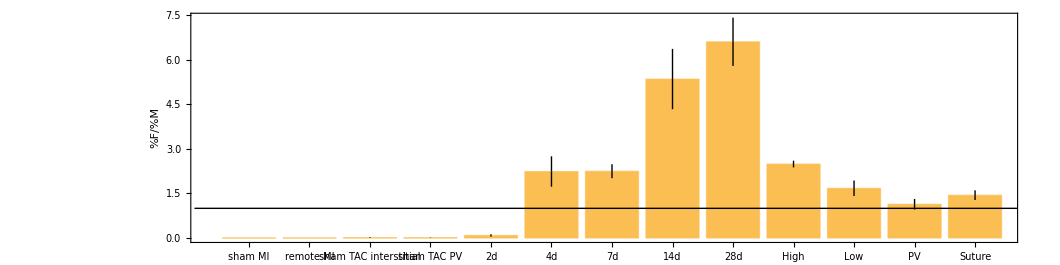

```mathematica
BarChart[#[[;;,1]],ChartLabels->StringReplace[#[[;;,2]]," "->"\n"],Frame->True,FrameLabel->{Automatic,"%F/%M"},RotateLabel->False,Epilog->{Thin,Line[{{0.1,1},{14,1}}]},AspectRatio->.25,FrameStyle->14]&@Join[
{(#[[1,1]])/(#[[1,2]]),#[[2]]}&/@((Reverse/@{
{"sham MI",#[[5,2,1,2]]},
{"remote MI",First@Median@(#[[{1,2,3,4,-1},2,;;,2]]/.Around[x_,_]:>x)},
{"sham TAC interstitial",#[[6,2,1,2]]},
{"sham TAC PV",#[[6,2,2,2]]}})&@({#[[1]],{#[[1]],Mean@#[[2]]}&/@#[[2]]}&/@DeleteCases[{#[[1]],ReverseSort@Cases[#[[2]],{"RZ"|"PV Sham",_}]}&/@Time,{_,{}}])),({Times@@(Mean[#[[1]](*/.Around[x_,y_]:>x*)]^{1,-1}),#[[2]]}&/@#&@Join[{#[[2,1,2]],#[[1]]}&/@Time[[{1,2,3,4,8}]],Reverse/@Time[[6,2]],Reverse/@Time[[8,2,{-1}]]])]
```

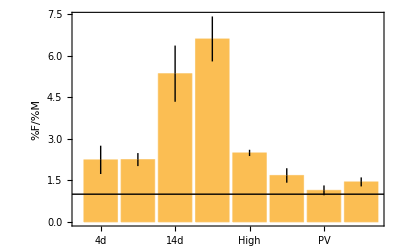

```mathematica
BarChart[#[[2;;,1]],ChartLabels->#[[2;;,2]],Frame->True,FrameLabel->{Automatic,"%F/%M"},RotateLabel->False,Epilog->{Thin,Line[{{0.2,1},{10,1}}]}]&@({Times@@(Mean[#[[1]]]^{1,-1}),#[[2]]}&/@#&@Join[{#[[2,1,2]],#[[1]]}&/@Time[[{1,2,3,4,8}]],Reverse/@Time[[6,2]],Reverse/@Time[[8,2,{-1}]]])
```

```mathematica
MICounts={#[[1,1,2]],{StringTake[#[[1,1]],2],#[[;;,2]]}&/@GatherBy[{#[[1,3]],#[[2]]}&/@#,StringTake[#[[1]],2]&]}&/@GatherBy[{#[[;;3]],{(Total@#)/0.16,N@{#,#/(Total@#)}ᵀ}&@Table[Count[#[[4,;;,1]],c],{c,{"F","M","C"}}]}&/@NCounts,#[[1,2]]&][[{1,2,3,4,8}]];
```

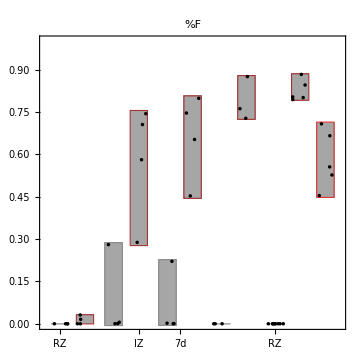
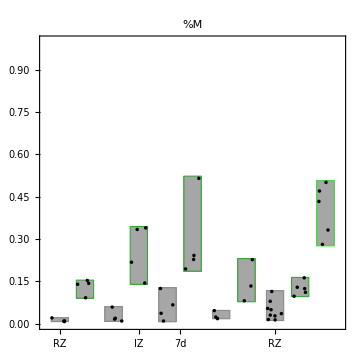

```mathematica
Row[
MapIndexed[
DistributionChart[Join[{#[[2]]},Delete[#,{2}]]&/@#,ChartElementFunction->"PointDensity",ChartLabels->{{"2d","4d","7d","14d","28d"},{"RZ","IZ","Suture"}},PlotRange->{0,1},PlotLabel->{"%F","%M"}[[#2[[1]]]],ChartStyle->Flatten[{Gray,{{Darker@Red,Red},{Darker@Green,Green}}[[#2[[1]]]]}],ImageSize->Medium,PlotRangePadding->Scaled[.01],AspectRatio->1]&,
((Transpose/@Map[Transpose,(Time[[{1,2,3,4,-1},2,;;,2]]/.Around[x_,y_]:>x),{2}])ᵀ)],
Spacer@10]
```

```mathematica
NCounts1=NCounts[[;;,{2,1,3,4}]]/.x_String:>Which[StringContainsQ[x,"Z"],StringTake[x,2],StringContainsQ[x,"Fibrosis"],StringSplit[x," "][[1]],StringContainsQ[x,"Suture"],StringSplit[x," "][[1]],StringContainsQ[x,"PV Sham"],StringJoin@@StringSplit[x," "][[;;2]],True,x];
```

```mathematica
NCounts2={#[[1,1,1]],{#[[1,1]],#[[;;,2]]}&/@GatherBy[Join@@(ReverseSort/@#[[;;,;;,2;;]]),First]}&/@((GatherBy[(NCounts1/.x:{{_String,_,_}..}:>N@Mean@x[[;;,-1]]),{#[[1]]&,#[[2]]&,#[[3]]&}][[{1,2,3,4,8,5,6,7}]]/.x:{{_String,_String,_String,_}..}:>{Sequence@@x[[1,{1,3}]],Mean@x[[;;,-1]]}));
```

```mathematica
datarule=(#[[1,1]]->(#[[1,1]]->(#[[1,1]]->Join@@#[[;;,2]]&/@GatherBy[#[[;;,2;;]],First])&/@GatherBy[#[[;;,2;;]],First])&/@GatherBy[NCounts1/.x:{{_String,_,_}..}:>x[[;;,-1]],First][[{1,2,3,4,8,5,6,7}]]);
```

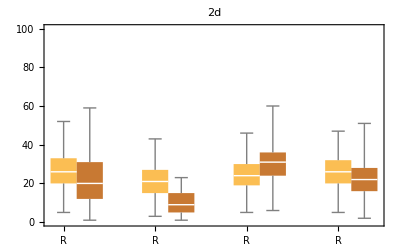
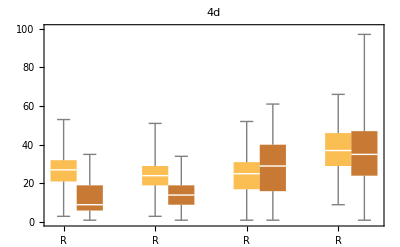
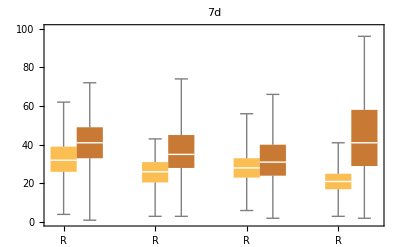
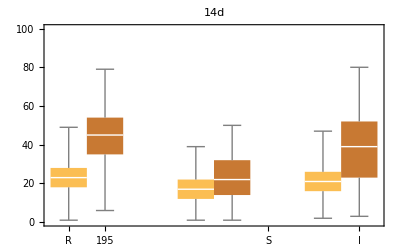
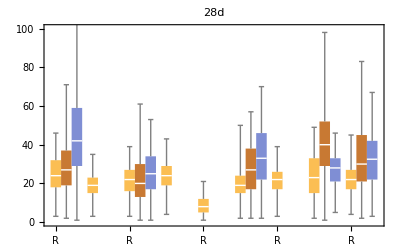

```mathematica
Table[BoxWhiskerChart[{"RZ","IZ","Suture"}/.(d/.datarule)[[;;,2]],ChartLabels->{(d/.datarule)[[;;,1]],{"R","I","S"}},PlotLabel->d,PlotRange->{0,100},BarSpacing->{0,.5}],{d,{"2d","4d","7d","14d","28d"}}]
```

```mathematica
Export["MI.xls","Sheets"->Thread[
{"2d","4d","7d","14d","28d"}->(Prepend[#,{"RZ","IZ","Suture"}]&/@(N@Table[
({"RZ","IZ","Suture"}/.(d/.datarule/.x:{_Integer..}:>Mean@x)[[;;,2]]),
{d,{"2d","4d","7d","14d","28d"}}]/._String:>NA))],"Rules"]
```

MI.xls

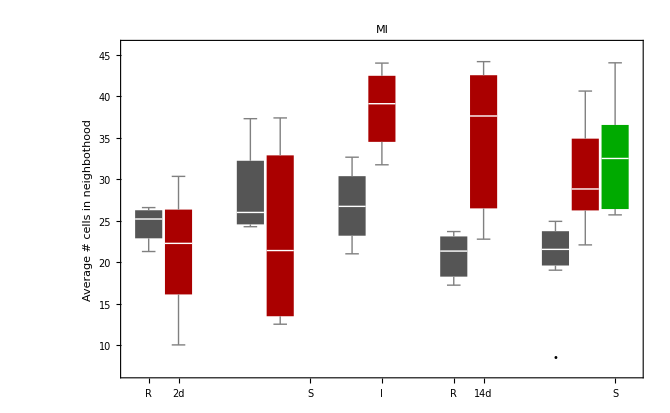

```mathematica
BoxWhiskerChart[
Table[
({"RZ","IZ","Suture"}/.(d/.datarule/.x:{_Integer..}:>Mean@x)[[;;,2]])ᵀ,
{d,{"2d","4d","7d","14d","28d"}}],
"Outliers",
ChartLabels->{{"2d","4d","7d","14d","28d","TAC"},{"R","I","S"}},
ChartStyle->Darker@{Gray,Red,Green},BarSpacing->{.1,.5},FrameLabel->{Automatic,"Average # cells in neighbothood"},PlotLabel->"MI"]
```

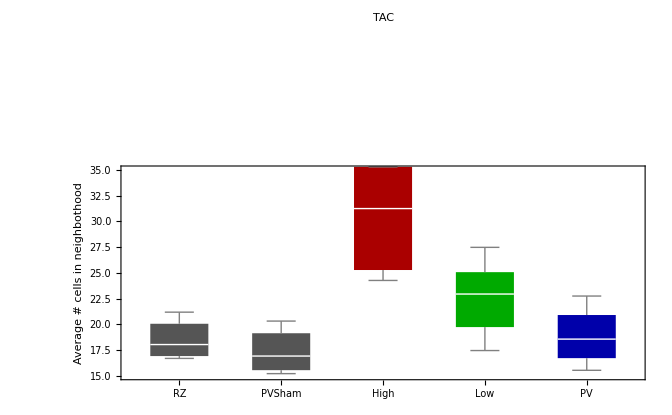

```mathematica
BoxWhiskerChart[
DeleteCases[
Join@@Table[({"RZ","PVSham","High","Low","PV"}/.(d/.datarule/.x:{_Integer..}:>Mean@x)[[;;,2]])ᵀ,{d,{"SHAM","TAC"}}],
{_String..}],

"Outliers",ChartLabels->{"RZ","PVSham","High","Low","PV"},

ChartStyle->Darker@{Gray,Gray,Red,Green,Blue},PlotRange->{15,35},FrameLabel->{Automatic,"Average # cells in neighbothood"},PlotLabel->"TAC"]
```

```mathematica
Export["TAC.xls",Flatten/@({{"RZ","PVSham","High","Low","PV"},DeleteCases[
Join@@Table[({"RZ","PVSham","High","Low","PV"}/.(d/.datarule/.x:{_Integer..}:>N@Mean@x)[[;;,2]])ᵀ,{d,{"SHAM","TAC"}}],
{_String..}]}ᵀ)]
```

TAC.xls

```mathematica
dataruledetail=(#[[1,1]]->(#[[1,1]]->(#[[1,1]]->Join@@#[[;;,2]]&/@GatherBy[#[[;;,2;;]],First])&/@GatherBy[#[[;;,2;;]],First])&/@GatherBy[NCounts1,First][[{1,2,3,4,8,5,6,7}]]);
```

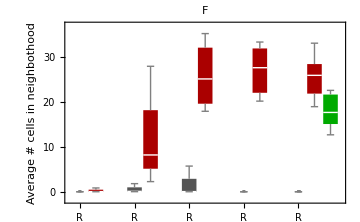
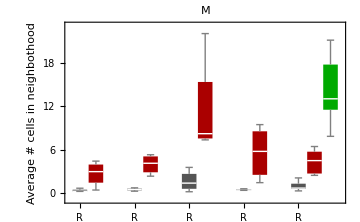
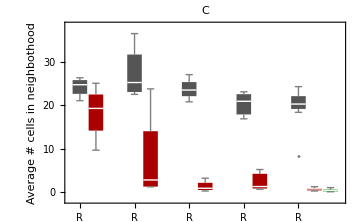
-Graphics--Graphics--Graphics-MI

```mathematica
Labeled[
Row[Table[
BoxWhiskerChart[
Table[
({"RZ","IZ","Suture"}/.(d/.dataruledetail/.x:{{_String,_,_}..}:>x[[;;,2]]/.x:{_Integer..}:>x[[c]]/.x:{_Integer..}:>Mean@x)[[;;,2]])ᵀ,
{d,{"2d","4d","7d","14d","28d"}}],
"Outliers",
ChartLabels->{{"2d","4d","7d","14d","28d","TAC"},{"R","I","S"}},
ChartStyle->Darker@{Gray,Red,Green},BarSpacing->{.1,.5},PlotLabel->{"F","M","C"}[[c]],FrameLabel->{Automatic,"Average # cells in neighbothood"},ImageSize->Medium],
{c,{1,2,3}}],Spacer@10],
Style["MI",20],Top]
```

```mathematica
Table[
Export["MI_"<>{"F","M","C"}[[c]]<>".xls",
"Sheets"->Thread[
{"2d","4d","7d","14d","28d"}->(Prepend[#,{"RZ","IZ","Suture"}]&/@(N@Table[
({"RZ","IZ","Suture"}/.(d/.dataruledetail/.x:{{_String,_,_}..}:>x[[;;,2]]/.x:{_Integer..}:>x[[c]]/.x:{_Integer..}:>N@Mean@x)[[;;,2]]),
{d,{"2d","4d","7d","14d","28d"}}]/._String:>NA))],
"Rules"],
{c,{1,2,3}}]
```

{MI_F.xls,MI_M.xls,MI_C.xls}

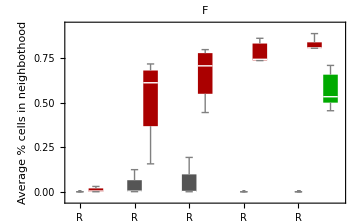
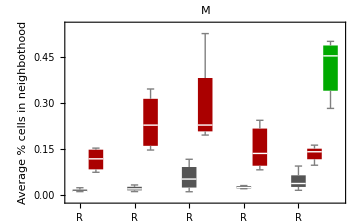
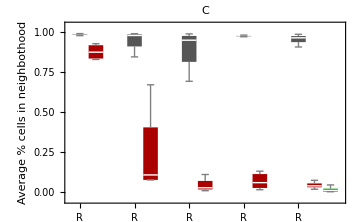
-Graphics--Graphics--Graphics-MI

```mathematica
Labeled[
Row[Table[
BoxWhiskerChart[
Table[
({"RZ","IZ","Suture"}/.(d/.dataruledetail/.x:{{_String,_,_}..}:>x[[;;,2]]/.x:{_Integer..}:>N@(x[[c]]/(Total@x))/.x:{_Real..}:>Mean@x)[[;;,2]])ᵀ,
{d,{"2d","4d","7d","14d","28d"}}],
"Outliers",
ChartLabels->{{"2d","4d","7d","14d","28d","TAC"},{"R","I","S"}},
ChartStyle->Darker@{Gray,Red,Green},BarSpacing->{.1,.5},PlotLabel->{"F","M","C"}[[c]],FrameLabel->{Automatic,"Average % cells in neighbothood"},ImageSize->Medium],
{c,{1,2,3}}],Spacer@10],
Style["MI",20],Top]
```

```mathematica
Table[
Export["MI_"<>{"%F","%M","%C"}[[c]]<>".xls",
"Sheets"->Thread[
{"2d","4d","7d","14d","28d"}->(Prepend[#,{"RZ","IZ","Suture"}]&/@(N@Table[
({"RZ","IZ","Suture"}/.(d/.dataruledetail/.x:{{_String,_,_}..}:>x[[;;,2]]/.x:{_Integer..}:>N@(x[[c]]/(Total@x))/.x:{_Real..}:>Mean@x)[[;;,2]]),
{d,{"2d","4d","7d","14d","28d"}}]/._String:>NA))],
"Rules"],
{c,{1,2,3}}]
```

{MI_%F.xls,MI_%M.xls,MI_%C.xls}

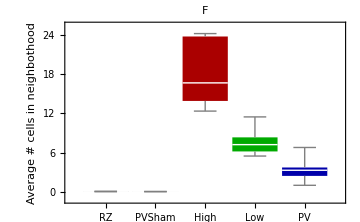
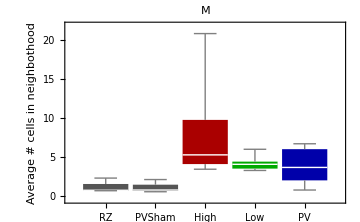
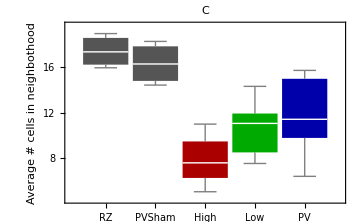
-Graphics--Graphics--Graphics-TAC

```mathematica
Labeled[
Row[
Table[
BoxWhiskerChart[
DeleteCases[
Join@@Table[
({"RZ","PVSham","High","Low","PV"}/.(d/.dataruledetail/.x:{{_String,_,_}..}:>x[[;;,2]]/.x:{_Integer..}:>x[[c]]/.x:{_Integer..}:>Mean@x)[[;;,2]])ᵀ,
{d,{"SHAM","TAC"}}],
{_String..}],
(*"Outliers",*)
ChartLabels->{"RZ","PVSham","High","Low","PV"},
ChartStyle->Darker@{Gray,Gray,Red,Green,Blue},BarSpacing->{.1,.5},PlotLabel->{"F","M","C"}[[c]],FrameLabel->{Automatic,"Average # cells in neighbothood"},ImageSize->Medium,PlotRange->All],
{c,{1,2,3}}],Spacer@10],
Style["TAC",20],Top]
```

```mathematica
Export["TAC_FMC.xls",
"Sheets"->Thread[{"F","M","C"}->(Flatten/@Thread[{{"RZ","PVSham","High","Low","PV"},#}]&/@Table[
DeleteCases[
Join@@Table[
({"RZ","PVSham","High","Low","PV"}/.(d/.dataruledetail/.x:{{_String,_,_}..}:>x[[;;,2]]/.x:{_Integer..}:>x[[c]]/.x:{_Integer..}:>N@Mean@x)[[;;,2]])ᵀ,
{d,{"SHAM","TAC"}}],
{_String..}],
{c,{1,2,3}}])],
"Rules"]
```

TAC_FMC.xls

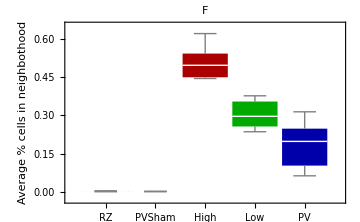
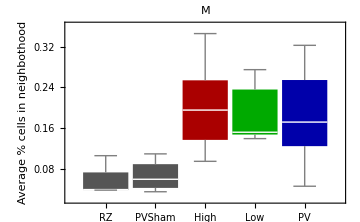
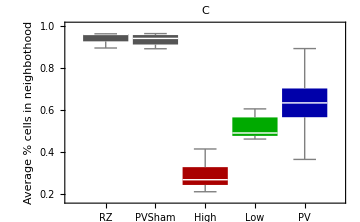
-Graphics--Graphics--Graphics-TAC

```mathematica
Labeled[
Row[Table[
BoxWhiskerChart[
DeleteCases[
Join@@Table[
({"RZ","PVSham","High","Low","PV"}/.(d/.dataruledetail/.x:{{_String,_,_}..}:>x[[;;,2]]/.x:{_Integer..}:>N@(x[[c]]/(Total@x))/.x:{_Real..}:>Mean@x)[[;;,2]])ᵀ,
{d,{"SHAM","TAC"}}],
{_String..}],
(*"Outliers",*)
ChartLabels->{"RZ","PVSham","High","Low","PV"},
ChartStyle->Darker@{Gray,Gray,Red,Green,Blue},BarSpacing->{.1,.5},PlotLabel->{"F","M","C"}[[c]],FrameLabel->{Automatic,"Average % cells in neighbothood"},ImageSize->Medium,PlotRange->All],
{c,{1,2,3}}],
Spacer@10],
Style["TAC",20],Top]
```

```mathematica
Export["TAC_FMC%.xls",
"Sheets"->Thread[{"%F","%M","%C"}->(Flatten/@Thread[{{"RZ","PVSham","High","Low","PV"},#}]&/@Table[
DeleteCases[
Join@@Table[
({"RZ","PVSham","High","Low","PV"}/.(d/.dataruledetail/.x:{{_String,_,_}..}:>x[[;;,2]]/.x:{_Integer..}:>N@(x[[c]]/(Total@x))/.x:{_Real..}:>Mean@x)[[;;,2]])ᵀ,
{d,{"SHAM","TAC"}}],
{_String..}],
{c,{1,2,3}}])],
"Rules"]
```

TAC_FMC%.xls

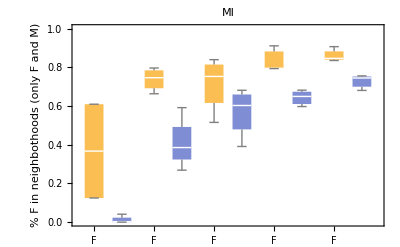

```mathematica
BoxWhiskerChart[
Table[
DeleteCases[
Table["IZ"/.(d/.DeleteCases[dataruledetail,{c|"C",__},∞]/.x:{_String,_,_}:>N@(x[[2,1]]/(Total@x[[2]]))/.x:{_Real..}:>Mean@x)[[;;,2]],{d,{"2d","4d","7d","14d","28d"}}],{}|"IZ",∞],{c,{"M","F"}}]ᵀ,
PlotRange->{0,1},PlotRangePadding->None,ChartLabels->{{"2d","4d","7d","14d","28d"},{"F","M"}},FrameLabel->{Automatic,"% F in neighbothoods (only F and M)"},
PlotLabel->"MI"
]
```

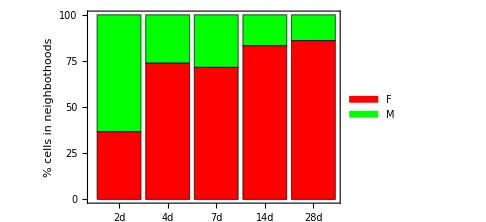
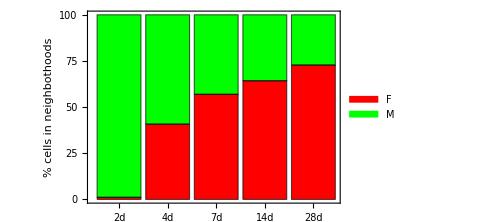
-Graphics--Graphics-MI

```mathematica
Labeled[Row[BarChart[{#,1-#}&/@#,ChartLayout->"Percentile",ChartStyle->{Red,Green},ChartLabels->{{"2d","4d","7d","14d","28d"},None},ChartLegends->Placed[{"F","M"},Below],FrameLabel->{Automatic,"% cells in neighbothoods"},Frame->True,PlotRangePadding->None,ImageSize->Medium]&/@Map[Mean,Table[
DeleteCases[
Table["IZ"/.(d/.DeleteCases[dataruledetail,{c|"C",__},∞]/.x:{_String,_,_}:>N@(x[[2,1]]/(Total@x[[2]]))/.x:{_Real..}:>Mean@x)[[;;,2]],{d,{"2d","4d","7d","14d","28d"}}],{}|"IZ",∞],{c,{"M","F"}}],{2}],
Spacer@10],Style["MI",24],Top]
```

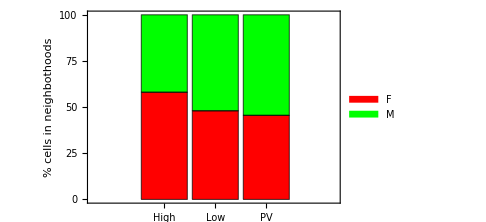
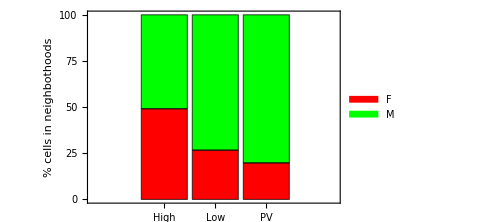
-Graphics--Graphics-TAC

```mathematica
Labeled[Row[BarChart[{#,1-#}&/@#,ChartLayout->"Percentile",ChartStyle->{Red,Green},ChartLabels->{{"High","Low","PV"},None},ChartLegends->Placed[{"F","M"},Below],FrameLabel->{Automatic,"% cells in neighbothoods"},Frame->True,PlotRangePadding->None,ImageSize->Medium]&/@Map[Mean,Table[
({"High","Low","PV"}/.("TAC"/.DeleteCases[dataruledetail,{c|"C",__},∞]/.x:{_String,_,_}:>N@(x[[2,1]]/(Total@x[[2]]))/.x:{_Real..}:>Mean@x)[[;;,2]])ᵀ,
{c,{"M","F"}}],
{2}],Spacer@10],Style["TAC",24],Top]
```

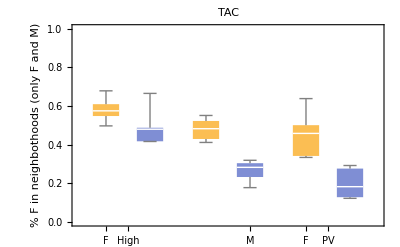

```mathematica
BoxWhiskerChart[
Table[
({"High","Low","PV"}/.("TAC"/.DeleteCases[dataruledetail,{c|"C",__},∞]/.x:{_String,_,_}:>N@(x[[2,1]]/(Total@x[[2]]))/.x:{_Real..}:>Mean@x)[[;;,2]])ᵀ,
{c,{"M","F"}}]ᵀ,
ChartLabels->{{"High","Low","PV"},{"F","M"}},PlotRange->{0,1},
FrameLabel->{Automatic,"% F in neighbothoods (only F and M)"},PlotLabel->"TAC"

]
```